# Mean-field theory for planar spins

Tom Jackson -- revised 6/4/12

```mathematica
FrontEndExecute[FrontEndToken["EvaluateInitialization"]];
```

## General code:

## Physical constants

Reference: 2011 CODATA values at http://pdg.lbl.gov/2011/reviews/rpp2011-rev-phys-constants.pdf

UNITS: Magnetic field in Tesla. Length in Angstroms; Mass & Time chosen so that energy units are meV and ℏ=1.
NOTE this means we don’t have the freedom to set c=1 as well! Below we convert c from m/sec to Å/[new time unit] using ℏ= 6.5...*10^(-22) MeV*sec = 1 meV * [new time unit].

```mathematica
ℏ=1;
𝒸=299792458*(1*^10)*((6.58211899*^-22)*1*^9);
```

Bohr magneton in meV/Tesla,
Nuclear magneton in meV/Tesla,
Boltzmann constant in meV/K:

```mathematica
μB=5.78838175*^-2;
μN=3.15245123*^-5;
𝓀B=8.617343*^-2;
```

Electron mass in [new mass unit] = meV * ([new time unit] / Å)^2,
Neutron mass in [new mass unit]
Electron g-factor (dimensionless)
Neutron magnetic moment

```mathematica
Clear[𝓂];
𝓂[e]=0.510998810*^9/𝒸^2;
𝓂[n]=939.565346*^9/𝒸^2;
electronℊ=2(1+1159.65218073*^-6);
neutronμ=-1.913042*μN;
```

## Definitions -- utility functions

```mathematica
replace[expn_,rules_List]:=
If[DeleteDuplicates[rules⟦All,0⟧]==={List},
Fold[ReplaceAll,expn,rules],
ReplaceAll[expn,rules]
];
```

```mathematica
CircleTimes=KroneckerProduct;
directProduct[v1_List,vv2_List]:=MapThread[Times,{v1,vv2}];
```

Define new notation for matrix operations: for matrices A,B,C... define A⊤B⊤C.. (with ⊤ being \ [DownTee], or EscdTEsc) to be the iterated conjugation ... C.B.A.Bᵀ.Cᵀ.... This is very nonstandard, but the infix notation makes it more convenient to enter.

```mathematica
DownTee[a_,bc__]:=Fold[#2.#1.Transpose[#2]&,a,{bc}];
```

```mathematica
cosExpand[expn_,patt_]:=(TrigExpand[ExpToTrig[expn]]/.
{Sin[patt]^(n_Integer):>(1-Cos[patt]^2)^(n/2)/;EvenQ[n]});
```

TODO: factor out overall monomial factor from expression (where RHS = 0) -- also handle lists, matrices

## Definitions -- Lattices and crystals

### Bravais lattices

```mathematica
Clear[basisVectors,reciprocalBasisVectors];
basisVectors[lattice_]:= unitBasisVectors[lattice]*latticeConstants[lattice];
reciprocalBasisVectors[lattice_]:=
2Pi*Transpose[Inverse[basisVectors[lattice]]];
```

```mathematica
primitiveCellFn[basisVects_,cutoff_]:=With[
{dim=Length[basisVects]},
Nearest[
Flatten[Array[
{N[List[##].basisVects]->List[##]}&,
ConstantArray[2cutoff+1,dim],
ConstantArray[-cutoff,dim]
]]
]];
toFirstBZ[lattice_,vec_]:=
{#,vec-#.N[reciprocalBasisVectors[lattice]]}&[
First[bzFunction[lattice][vec]]
];
```

### Crystal systems

Note: the ?AtomQ test is necessary to enable different behavior for lattices defined with the supercell command (below).

```mathematica
dimension[crystal_?AtomQ]:=dimension[bravaisLattice[crystal]];
unitBasisVectors[crystal_?AtomQ]:=unitBasisVectors[bravaisLattice[crystal]];
latticeConstants[crystal_?AtomQ]:=latticeConstants[bravaisLattice[crystal]];
bzFunction[crystal_?AtomQ,vec_]:=bzFunction[bravaisLattice[crystal,vec]];
```

```mathematica
ClearAll[basis,nearestNeighbors,nBasis];
Rule[±x_,i_]^:=Sequence[Rule[x,i],Rule[-x,i]];
basisLabels[crystal_]:=basisOffsets[crystal]⟦All,1⟧;
basis[crystal_,cell_List:{}]:=With[
{cell2=If[cell==={},ConstantArray[0,dimension[crystal]],cell]},
Rule[cell2,#]&/@basisLabels[crystal]
];
nBasis[crystal_]:=Length[basisOffsets[crystal]];
nearestNeighbors[crystal_,Rule[lattIndices_,basisElt_]]:=
Rule[lattIndices+#1,#2]&@@@nearestNeighbors[crystal,basisElt];
```

```mathematica
Clear[latticeℛ,latticeΔℛ,ℛ,Δℛ];
latticeℛ[crystal_,0]:=ConstantArray[0,dimension[crystal]];
latticeℛ[crystal_,basisElt_List]:=
If[First[basisElt]==0,
ConstantArray[0,dimension[crystal]],
(basisElt/.basisOffsets[crystal])
];
latticeℛ[crystal_,Rule[lattIndices_,basisElt_]]:=
lattIndices+latticeℛ[crystal,basisElt];
latticeΔℛ[crystal_,pos1_Rule,pos2_Rule]:=
latticeℛ[crystal,pos1]-latticeℛ[crystal,pos2];
ℛ[crystal_,latticePosition_]:=
latticeℛ[crystal,latticePosition].basisVectors[crystal];
Δℛ[crystal_,pos1_Rule,pos2_Rule]:=
ℛ[crystal,pos1]-ℛ[crystal,pos2];
SetAttributes[ℛ,Listable];
SetAttributes[Δℛ,Listable];
```

### Supercells (multiples of crystal unit cell)

TODO: need bzFunction for this case

```mathematica
ClearAll[supercell];
dimension[supercell[crystal_,_]]:=dimension[bravaisLattice[crystal]];
unitBasisVectors[supercell[crystal_,_]]:=unitBasisVectors[bravaisLattice[crystal]];
latticeConstants[supercell[crystal_,dupes_]]:=dupes*latticeConstants[bravaisLattice[crystal]];
supercell/:basisOffsets[supercell[crystal_,dupes_]]:=
With[
{dim=dimension[crystal]},
Flatten[Outer[
Rule[Join[#1⟦1⟧,#2],(#1⟦2⟧+#2)/dupes]&,
basisOffsets[crystal],
Flatten[Array[List,dupes,ConstantArray[0,dim]],dim-1],
1]]
];
supercell/:nearestNeighbors[supercell[crystal_,dupes_],basisElt_]:=
nearestNeighbors[supercell[crystal,dupes],Rule[0,basisElt]];
supercell/:nearestNeighbors[supercell[crystal_,dupes_],Rule[lattIndices_,basisElt_]]:=
Rule[
lattIndices+MapThread[Quotient,{Rest[basisElt]+#1,dupes}],
Join[#2,
MapThread[Mod,{Rest[basisElt]+#1,dupes}]
]
]&@@@nearestNeighbors[crystal,{First[basisElt]}];
```

```mathematica
removeSupercell[expn_,dupes_]:=(Times@@dupes)*expn/.(b:op)[Rule[x_,basis_]]:>b[(dupes*x+Rest[basis])->{First[basis]}];
```

### General definitions

```mathematica
Clear[n𝓆,latticeγ];
n𝓆[q_,lattice_]:=
Plus@@(2Pi*q*Transpose[Inverse[
(#*latticeConstants[lattice])&/@ unitBasisVectors[lattice]
]]);
latticeγ[crystal_,basisSite_]:=
Expand[TrigExpand[ExpToTrig[
(1/Length[nearestNeighbors[crystal,basisSite]])Total[
Exp[I*𝓆[#]]&/@
((latticeℛ[crystal,#]-latticeℛ[crystal,basisSite])&/@
nearestNeighbors[crystal,basisSite])
]
]]/.
{Sin[x_]^(n_Integer):>(1-Cos[x]^2)^(n/2)/;EvenQ[n]}
];
```

## Example -- Honeycomb crystal system

To illustrate the use of the functions from the previous section, we look at the honeycomb crystal (which makes a non-trivial example since it has a two-atom basis).

Note that we use the ^=, ^:= and /: operators to make assignments here, instead of = and :=. More information can be found in Mathematica’s help pages, but briefly stated the difference is that the difference between saying f[a] = 3 and f[a]^=3 is that the former stores the definition in the function f, but the latter stores it in the argument a.

#### Defining the underlying Bravais lattice:

```mathematica
Clear[𝔞,hexagonal];
dimension[hexagonal]^=2;
unitBasisVectors[hexagonal]^={{1,0},{Cos[Pi/3],Sin[Pi/3]}};
latticeConstants[hexagonal]^={𝔞,𝔞};
N[𝔞]=1.5;
bzFunction[hexagonal]^=primitiveCellFn[reciprocalBasisVectors[hexagonal],5];
```

#### Defining the crystal itself:

```mathematica
Clear[honeycomb];
bravaisLattice[honeycomb]^=hexagonal;
basisOffsets[honeycomb]^={
{1}->(1/3){1,1},
{2}->(2/3){1,1}
};
honeycomb/:nearestNeighbors[honeycomb,{1}]:=
{{0,0}->{2},{-1,0}->{2},{0,-1}->{2}};
honeycomb/:nearestNeighbors[honeycomb,{2}]:=
{{0,0}->{1},{1,0}->{1},{0,1}->{1}};
```

#### Format for positions in the crystal

The convention we use is that atoms/points in a crystal are specified by an expression of the form {n_1,n_2,..., n_d} → {b}, where the {n_i} are integers specifying the cell of the Bravais lattice containing the point, and b is a number or list specifiying which basis atom within that cell we’re talking about. Specifying the information this way makes it easy to, e.g, compute the nearest neighbors of an atom or define operators that act differently on different sublattices.

Given a point in the specification above, we’ve defined three ways to convert it into a geometric position vector. The function latticeℛ returns the position vector of the point as multiples of the Bravais lattice basis vectors. The function ℛ gives the position vector as an actual distance vector (as a symbolic expression involving the Bravias lattice constants), and finally N[ℛ[#]] gives the numeric position of the point in Angstroms (using the numerical values of the lattice constants defined in the Bravais lattice).  Note that ℛ automatically applies itself to each element of a list of points.

```mathematica
pt={-1,2}->{2};
latticeℛ[honeycomb,pt]
ℛ[honeycomb,pt]
N[ℛ[honeycomb,pt]]
```

{-1/3,8/3}

{𝔞,(4 𝔞)/(√3)}

{1.5,3.4641}

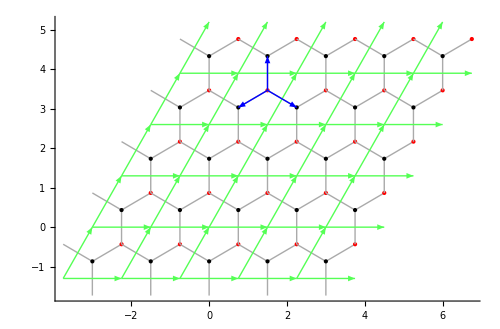

```mathematica
Show[Graphics[N[
Flatten[Table[{
Lighter[Gray],
Flatten[
Line[{ℛ[honeycomb,{i,j}->{1}],ℛ[honeycomb,#]}]&/@nearestNeighbors[honeycomb,{i,j}->{1}]
],
Black,Point[ℛ[honeycomb,{i,j}->{1}]],
Red,Point[ℛ[honeycomb,{i,j}->{2}]],
Lighter[Green],
Arrow[{ℛ[honeycomb,{i,j}->0],ℛ[honeycomb,{i+1,j}->0]}],
Arrow[{ℛ[honeycomb,{i,j}->0],ℛ[honeycomb,{i,j+1}->0]}]
},
{i,-2,2},{j,-1,3}]]~Join~{Blue}~Join~
Flatten[
Arrow[{ℛ[honeycomb,pt],ℛ[honeycomb,#]}]&/@
nearestNeighbors[honeycomb,pt]
]
]],
Axes->True,
ImageSize->500]
```

#### Defining supercells

```mathematica
honeycomb2=supercell[honeycomb,{2,1}];
basis[honeycomb2]
basisOffsets[honeycomb2]
nearestNeighbors[honeycomb2,{2,1,0}]
nearestNeighbors[honeycomb2,{-2,-1}->{2,1,0}]
```

{{0,0}→{1,0,0},{0,0}→{1,1,0},{0,0}→{2,0,0},{0,0}→{2,1,0}}

{{1,0,0}→{1/6,1/3},{1,1,0}→{2/3,1/3},{2,0,0}→{1/3,2/3},{2,1,0}→{5/6,2/3}}

{{0,0}→{1,1,0},{1,0}→{1,0,0},{0,1}→{1,1,0}}

{{-2,-1}→{1,1,0},{-1,-1}→{1,0,0},{-2,0}→{1,1,0}}

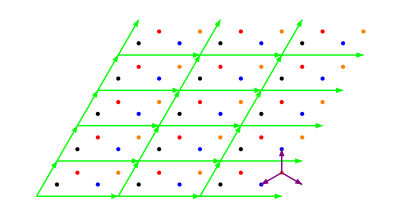

```mathematica
Show[Graphics[N[
Flatten[Table[
{Green,
Arrow[{ℛ[honeycomb2,{i,j}->0],ℛ[honeycomb2,{i+1,j}->0]}],
Arrow[{ℛ[honeycomb2,{i,j}->0],ℛ[honeycomb2,{i,j+1}->0]}]}
~Join~Riffle[
{Black,Blue,Red,Orange},
(Point[ℛ[honeycomb2,{i,j}->#]]&/@basis[honeycomb2]⟦All,2⟧)
],
{i,-1,1},{j,-1,3}]]~Join~{Purple}~Join~
Flatten[
Arrow[{
ℛ[honeycomb2,{1,-1}->{2,1,0}],
ℛ[honeycomb2,#]}]&/@nearestNeighbors[honeycomb2,{1,-1}->{2,1,0}]
]
]]]
```

## Definitions -- Second-quantized boson operators

Convention: we treat any symbol of the form X̂, ie OverHat[X], as an operator with potentially non-trivial commutation relations. Arguments (postions, momenta, flavor indices) are specified like arguemnts to a function, ie OverHat[b][k,s]. Creation operators are denoted by OverHat[SuperDagger[X]]. All this is kept as general as possible, in case we e.g. want to work with both boson and fermion ops in a future project.

We keep track of the nontrivial commutation relations by connecting boson operators with NonCommutativeMultiply. Define ExpandNCM as an extension of Expand which knows about non-commutative multiplication and treats all c-number factors in an expression appropriately.

TODO: add Interpretation statements to allow copy & base of operators from output form into input

```mathematica
Clear[cr,an];
Format[cr[h_],StandardForm]:=SuperDagger[OverHat[h]];
Format[cr[h_][i_],StandardForm]:=SuperDagger[OverHat[h]][i];
Format[cr[h_][Rule[x_,i_]],StandardForm]:=Subsuperscript[OverHat[h],i,†][Sequence@@x];
Format[an[h_],StandardForm]:=OverHat[h];
Format[an[h_][i_],StandardForm]:=OverHat[h][i];
Format[an[h_][Rule[x_,i_]],StandardForm]:=
Subscript[OverHat[h],i][Sequence@@x];
```

```mathematica
Clear[opHead,opCreate,opAnnihilate,op];
opHead=(cr|an);
opCreate=cr[_]|cr[_][__];
opAnnihilate=an[_]|an[_][__];
op=opCreate|opAnnihilate;
containsOpQ[expn_]:=(Count[{expn},op,Infinity]!=0);
opSign[op:opCreate]=-1;
opSign[op:opAnnihilate]=1;
opSign[op:Except[op]]=0;
hermitianConjugate[expn_]:=
ComplexExpand[Conjugate[
((expn/.{cr->an,an->cr})/.
NonCommutativeMultiply[ops__]:>
NonCommutativeMultiply@@Reverse[{ops}])
]];
```

```mathematica
Clear[ExpandNCM,ExpandAllNCM,CollectNCM];
ExpandNCM[(h:NonCommutativeMultiply)[a___,0,c___]]:=0;
ExpandNCM[(h:NonCommutativeMultiply)[a___,b_Plus,c___]]:=Distribute[h[a,b,c],Plus,h,Plus,ExpandNCM[h[##]]&];
ExpandNCM[(h:NonCommutativeMultiply)[a___,b_Times,c___]]:=ExpandNCM[h[a,Apply[NonCommutativeMultiply,b],c]];
ExpandNCM[(h:NonCommutativeMultiply)[a___,b:Except[op],c___]]:=b*ExpandNCM[h[a,c]];
ExpandNCM[(h:NonCommutativeMultiply)[a_]]:=a;
ExpandNCM[(h:NonCommutativeMultiply)[]]=1;
ExpandNCM[a_]:=Expand[a];
ExpandAllNCM[expn_]:=
Expand[MapAt[ExpandNCM,expn,Position[expn,NonCommutativeMultiply[___]]]];
CollectNCM[expn_]:=
Collect[ExpandAllNCM[expn],op|NonCommutativeMultiply[__]];
```

Patterns which match creation and annihilation operators, both with and without arguments. opSign = 1 for annihilation operators, = -1 for creation operators.

Cases considered by normOrderedQ : 1)  puts all ann. ops before cr. ops., 2) does nothing if two adjacent ops are identical, 3) sorts two ann ops (or two cr. ops) by reverse lex order in their labels, ie a^hat[ ...] gets put before b^hat[ ...] before cHat[ ...], etc. The exact details of the ordering in 3) don' t matter, so long as we pick some canonical order for all operators, which is done by opLabel.

Default behavior for the (generalized) commutator is to assume that any operators with different indices (of any kind) commute, but this can be overridden by supplying a new function commuteQ.

```mathematica
opLabel[opHead[h_]]:={h};
opLabel[opHead[h_][i_]]:=Flatten[{h,i}];
opLabel[opHead[h_][Rule[x_,i_]]]:=Flatten[{h,i,Expand[x]}];
normalOrderedQ[(op1:op),(op2:op)]:=
Which[
opSign[op1]!=opSign[op2],opSign[op1]<opSign[op2],
opLabel[op1]===opLabel[op2],True,
True,
Position[
{OrderedQ[#],OrderedQ[Reverse[#]]}&/@
Transpose[PadRight[{opLabel[op1],opLabel[op2]}]],
False,2,1]⟦1,2⟧==1
];
defaultCommuteQ[op1:op,op2:op]:=opLabel[op1]===opLabel[op2];
commutator[(op1:op),(op2:op),nonCommuteQ_:defaultCommuteQ]:=
If[opSign[op1]≠opSign[op2]&&nonCommuteQ[op1,op2],
opSign[op1],0];
normalOrder[expn_,nonCommuteQ_:defaultCommuteQ]:=
ExpandAllNCM[
ExpandAllNCM[expn]//.{
NonCommutativeMultiply[a___,(op1:op),(op2:op),c___]:>
Distribute[
 NonCommutativeMultiply[a,
statisticsSign[op1,op2](op2**op1)+commutator[op1,op2,nonCommuteQ],
c]]/;!normalOrderedQ[op1,op2]
}];
statisticsSign[(op1:op),(op2:op)]:=
statisticsSign[First[opLabel[op1]],First[opLabel[op2]]];
```

Definitions specific to boson operators:

```mathematica
gBosonHeadsList={b};
statisticsSign[x_,y_]:=1/;(MemberQ[gBosonHeadsList,x]||MemberQ[gBosonHeadsList,y]);
bosonHead=Alternatives@@Join[an/@gBosonHeadsList,cr/@gBosonHeadsList];
boson=bosonHead|bosonHead[__];
bosonQ[op1:op]:=MemberQ[gBosonHeadsList,First[opLabel[op1]]];
```

(If our problem involved fermions as well, we’d define them using)

```mathematica
gFermionHeadsList={c};
statisticsSign[x_,y_]:=-1/;(MemberQ[gFermionHeadsList,x]&&MemberQ[gFermionHeadsList,y]);
fermionHead=Alternatives@@Join[an/@gFermionHeadsList,cr/@gFermionHeadsList];
fermion=fermionHead|fermionHead[__];
fermionQ[op1:op]:=MemberQ[gFermionHeadsList,First[opLabel[op1]]];
```

After we’ve done all the operations that depend on the boson operators’ nontrivial commutation relations, return the coefficients of terms linear in bosons (to verify that we’re perturbing around a real ground state) and quadratic in bosons (to diagonalize, below).

```mathematica
operatorTruncate[expn_,nSpec_]:=With[
{kRange=Switch[nSpec,
List[_Integer],nSpec,
_Integer,Range[0,nSpec],
List[_Integer,_Integer],Range@@nSpec
]},
If[Length[kRange]==1,First[#],#]&@Collect[
Table[
Select[
ExpandAllNCM[expn],
Count[#,op,Infinity]==k&],
{k,kRange}],
op|NonCommutativeMultiply[__]]
];
quadraticApprox[expn_,nonCommuteQ_:defaultCommuteQ]:=operatorTruncate[normalOrder[expn,nonCommuteQ],2];
```

```mathematica
Clear[latticeBosonVector,linearCoeffs];
latticeBosonVector[crystal_,cell_List:{}]:=With[
{cell2=If[cell==={},ConstantArray[0,dimension[crystal]],cell]},
Flatten[Transpose[
{cr[b][#],an[b][#]}&/@
SortBy[basis[crystal,cell2],Last]
]]
];
linearCoeffs[expn_]:=With[
{flavorsOnly=expn/.(h:op)[Rule[x_,i_]]:>h[i]},
{
Coefficient[flavorsOnly,cr[b][#]]&/@
Sort[basisLabels[gCrystal]],
Coefficient[flavorsOnly,an[b][#]]&/@
Sort[basisLabels[gCrystal]]
}
];
```

```mathematica
Clear[momentumBosonVector,quadraticCoeffs];
momentumBosonVector[crystal_]:=
Flatten[MapAt[Reverse,
Transpose[
{cr[b][Rule[#,-𝓆]],cr[b][Rule[#,𝓆]],an[b][Rule[#,-𝓆]],an[b][Rule[#,𝓆]]}&/@
Sort[basisLabels[crystal]]
],
{{1},{3}}
]];
quadraticCoeffs[expn_]:=With[
{ops=momentumBosonVector[gCrystal]},
Outer[
Coefficient[expn,NonCommutativeMultiply[#1,#2]]&,
ops,ops
]];
```

```mathematica
listAllOps[expn_]:=
MapAt[
Flatten[Thread/@Through[{cr,an}[#]]]&,
Sort[DeleteDuplicates[#]]&/@Transpose[
Cases[expn,opHead[op_][arg_]:>{op,arg},Infinity]
],
1];
```

## Definitions -- Terms in Hamiltonian

### General forms for interactions between lattice degrees of freedom

```mathematica
Clear[singleSiteOp,nearestNeighborOp];
singleSiteOp[fn_]:=
(1/nBasis[gCrystal])Total[
fn[#]&/@basis[gCrystal]
];
nearestNeighborOp[fn_]:=
(1/(2nBasis[gCrystal]))ReleaseHold[
Total[Flatten[
Thread/@(
Hold[fn][#,nearestNeighbors[gCrystal,#]]&/@
basis[gCrystal]
)
]]
];
```

kthNearestNeighbors recursively makes a list of k-th nearest neighbors of a given site. finiteRangeOp defines a two-site operator whose range extends to the nnCutoff-th nearest neighbors of the site.

```mathematica
kthNearestNeighbors[k_Integer:1,Rule[x_,i_]]:=
If[k==0,Rule[x,i],
DeleteDuplicates[Flatten[
kthNearestNeighbors[k-1,gCrystal,Rule[x+#1,#2]]&@@@
nearestNeighbors[gCrystal,i]
]]
];
finiteRangeOp[nnCutoff_,fn_]:=
(1/(2nBasis[gCrystal]))*
Plus@@(
Map[Function[{site1},
Map[Function[{site2},
fn[site1,site2]],
DeleteCases[DeleteDuplicates[
Expand//@Flatten[Table[
kthNearestNeighbors[k,site1],
{k,1,nnCutoff}]
]],site1]
]],
basis[gCrystal]]//Flatten);
```

### Quantum spin-𝓈 operator in terms of Holstein-Primakoff bosons

Vacuum of H-P bosons corresponds to spin pointing along the +z axis. Rotate the local coordinate system of each spin so that this is along the direction of the classical ground state spin configuration (given by ϕ,θ below). We work within the approximation of noninteracting spin waves, so to get the quadratic Hamiltonian it suffices to expand the H-P operators to quadratic order in the bosons.

Choose (nonstandard) Euler angle convention so that the local Z axis is rotated to the direction specified by the vector in σcl:

```mathematica
eulerAngleRotation[{ϕ_,θ_,ψ_},vec_]:=
RotationMatrix[ϕ+Pi/2,{0,0,1}].
RotationMatrix[-θ+Pi/2,{1,0,0}].
RotationMatrix[ψ+Pi/2,{0,0,1}].vec;
```

```mathematica
eulerAngleRotation[{ϕ,θ,ψ},{0,0,1}]
```

{Cos[θ] Cos[ϕ],Cos[θ] Sin[ϕ],Sin[θ]}

```mathematica
Clear[hpSpinVector];
hpSpinVector[site_]:=
{{1,1,0}/2,{-I,I,0}/2,{0,0,1}}.
{
Sqrt[2𝓈]an[b][site],
Sqrt[2𝓈]cr[b][site],
𝓈-cr[b][site]**an[b][site]
};
```

TODO: add Interpretation statements to allow copy & base of dummy spin operators from output form into input

```mathematica
Clear[σ,S];
Format[S[Rule[x_,i_]],StandardForm]:=
Subscript[S,i][Sequence@@x];
Format[S[α_,Rule[x_,i_]],StandardForm]:=
Subsuperscript[S,i,α][Sequence@@x];
σ[i_List]:=σ[Rule[0,i]];
σ[i_Integer]:=σ[Rule[0,{i}]];
σ[Rule[v_,i_List]]:=
Switch[gSpins,
Classical,
eulerAngleRotation[{ϕ@@i,θ@@i,0},{0,0,1}],
Quantum,
eulerAngleRotation[{ϕ@@i,θ@@i,0},hpSpinVector[Rule[v,i]]],
_,
(S[#,Rule[v,i]]&/@{x,y,z})
];
```

### Operators in Hamiltonian

TODO : verify factors of s here -- still seems weird

```mathematica
σclFactor[n_Integer]:=
If[gSpins===Classical,
Which[n==1,𝓈+1,
n==2,𝓈(𝓈+1),
True,Pochhammer[𝓈,n]
],
1];
```

Noncommutative versions of vector products (for vectors whose entries contain boson operators):

```mathematica
dotNCM[v1_,v2_]:=If[
containsOpQ[v1]&&containsOpQ[v2],
Inner[NonCommutativeMultiply,v1,v2,Plus],
Dot[v1,v2]
];
crossNCM[v1_,v2_]:=If[
containsOpQ[v1]&&containsOpQ[v2],
Inner[NonCommutativeMultiply,LeviCivitaTensor[3].v2,v1,Plus],
Cross[v1,v2]
];
```

#### Single-site operators

Zeeman: usual H · S_i
Anisotropic Zeeman: From Phys. Rev. B 84, 224419 (2011): crystal symmetries allow a non-vanishing, non-diagonal component of the Zeeman tensor proportional to H^x S_i^y - H^y S_i^x for spins on the first sublattice and -(H^x S_j^y - H^y S_j^x) for spins on the second sublattice.
Easy-plane (in the lattice 𝔞-𝔟 plane): (S_i^z)^2, all sites

```mathematica
Clear[zeeman,anisotropicZ,easyPlane];
zeeman[magneticField_List]:=
σclFactor[1]*singleSiteOp[
Function[{site},
magneticField.σ[site]
]];
anisotropicZ[magneticField_List,axis_List:{0,0,1}]:=
σclFactor[1]*singleSiteOp[
Function[{site},
sublatticeSign[site]*axis.Cross[magneticField,σ[site]]
]];
easyPlane[norm_List:{0,0,1}]:=
σclFactor[2]*singleSiteOp[
Function[{site},
ExpandNCM[(σ[site].norm)**(σ[site].norm)]
]];
```

#### Two-site operators

Dzyaloshinski-Moriya: From Phys. Rev. B 84, 224419 (2011): because of the crystal’s symmetries, the D-M vector must be along the 𝔠 lattice direction, and the interaction must be proportional to S_i^x S_j^y - S_i^y S_j^x for nearest-neighbor spins <i,j>, with i in the first sublattice and j in the second.

```mathematica
Clear[dzyaloshinskiMoriya];
dzyaloshinskiMoriya[axis_List:{0,0,1}]:=
σclFactor[2]*nearestNeighborOp[
Function[{site1,site2},
If[sameSublatticeQ[site1,site2],0,
sublatticeSign[site1]*dotNCM[axis,crossNCM[σ[site1],σ[site2]]]
]
]];
```

We’ve been considering many different kinds of anisotropy for the exchange couplings, and for simplicity I wanted to collect them all in a single function. The exchange couplings couplings for the function planarHeisenberg can be specified in one of four formats, depending on the dimensions of the list given:
J : completely isotropic exchange
{J^(1), J^(2)} : Exchange couplings of the form J^(1) S_i · S_j for spins in the same lattice 𝔞-𝔟 plane, and J^(2) S_i · S_jfor spins in different planes, for nearest neighbor spins <i,j>
{J_x, J_y, J_z}: Exchange couplings of the form J_x S_i^x · S_j^x +  J_y S_i^y · S_j^y +  J_z S_i^z · S_j^z for all nearest neighbor spins <i,j>
{{J_x^(1), J_y^(1), J_z^(1)},{J_x^(2), J_y^(2), J_z^(2)}}: combination of the previous two types of anisotropy.

```mathematica
Clear[heisenberg,planarHeisenberg];
heisenberg[couplings_]:=
With[{
jxyz=Switch[Dimensions[couplings],
{3},couplings,
{},couplings*{1,1,1},
_,{1,1,1}
]},
σclFactor[2]*nearestNeighborOp[
Function[{site1,site2},
dotNCM[σ[site1].DiagonalMatrix[jxyz],σ[site2]]
]]
];
planarHeisenberg[couplings_]:=
With[{
j12xyz=Switch[Dimensions[couplings],
{2,3},couplings,
{3},{couplings,couplings},
{2},couplings⊗{1,1,1},
{},couplings*{{1,1,1},{1,1,1}},
_,{{1,1,1},{1,1,1}}
]},
σclFactor[2]*nearestNeighborOp[
Function[{site1,site2},
If[samePlaneQ[site1,site2],
dotNCM[σ[site1].DiagonalMatrix[j12xyz⟦1⟧],σ[site2]],
dotNCM[σ[site1].DiagonalMatrix[j12xyz⟦2⟧],σ[site2]]
]]]
];
```

Dipole-dipole: The following approximates the magnetic dipole-dipole interaction by truncating it at a finite range (considering interactions only out to nnCutoff-th nearest neighbors). This is a slow and inaccurate way to treat truly long-range interactions -- we should be doing this in Fourier space.

```mathematica
ℛij[rule1_,rule2_]:=
ℛ[gCrystal,rule1]-ℛ[gCrystal,rule2];
normℛij[rule1_,rule2_]:=
(Norm[ℛij[rule1,rule2]]/.Abs[x_]:>x);
dipoleDipole[nnCutoff_]:=
σclFactor[2]*finiteRangeOp[nnCutoff,
Function[{site1,site2},
dotNCM[σ[site1],σ[site2]]/normℛij[site1,site2]^3-
(3/normℛij[site1,site2]^5)*((σ[site1].ℛij[site1,site2])**(σ[site2].ℛij[site1,site2]))
]];
```

## Definitions -- Symplectic diagonalization/spectrum

### quadratic Hamiltonian in momentum space

for future ref: splitting the momentum sum (the two terms in each case) of quad boson fourier is necessary, otherwise we don’t get all the species (coefficient matrix isn’t even-dimensional). 
quad boson sym is necessary since otherwise diagonal blocks of the coeff matrix (ie the non boson # conserving ops)  aren’t diagonal.

TODO: make this faster: if we only care about the quadratic part, can skip right to the coefficient matrix & symmetrize that instead of working w boson operators.

```mathematica
Clear[quadraticBosonSym,quadraticBosonFourier];
quadraticBosonSym[expn_,nonCommuteQ_:defaultCommuteQ]:=
Transpose[
(#/.NonCommutativeMultiply[(b1:boson),(b2:boson)]:> 
(1/2){commutator[b1,b2,nonCommuteQ],b1**b2+b2**b1})&/@
(List@@expn)
];
quadraticBosonFourier[expn_,q_List]:=
ExpandAllNCM[expn]/.
NonCommutativeMultiply[
(b1:bosonHead)[Rule[δi_,i_]],(b2:bosonHead)[Rule[δj_,j_]]
]:>With[
{𝓆δij=2Pi*opSign[b1]*
(q.latticeΔℛ[gCrystal,Rule[δi,i],Rule[δj,j]])},
(nBasis[gCrystal]/2)If[
opSign[b1]==opSign[b2],
Exp[I*𝓆δij](b1[i->𝓆]**b2[j->-𝓆])
+Exp[-I*𝓆δij](b1[i->-𝓆]**b2[j->𝓆]),
Exp[I*𝓆δij](b1[i->𝓆]**b2[j->𝓆])
+Exp[-I*𝓆δij](b1[i->-𝓆]**b2[j->-𝓆])
]
];
```

Basic matrices for doing symplectic stuff. Ω is the symplectic unit; here we use the convention that it’s equal to (0 | I_n
-I_n | 0). Γ is a unitary change of basis to “real” position/momentum-like operators: Γ(OverHat[b^†]
b̂)=(p̂
q̂) . The symplectic transpose of a matrix M is Ω Mᵀ Ωᵀ; by analogy with the real and hermitian transposes for symmetric and hermitian matrices, a matrix is symplectic if it’s equal to its symplectic transpose. 
symplecticBasisPerm gives a permutation matrix P that transfers between the two conventions for the symplectic unit: P. diag[(0 | 1
-1 | 0),... , (0 | 1
-1 | 0)] .Pᵀ=Ω. We need it because the Schur decomposition is block diagonal -- ie SchurDecomposition returns diag[(0 | 1/ν_1
-1/ν_1 | 0),... , (0 | 1/ν_n
-1/ν_n | 0)], and we want these values in the form  (0 | diag{1/ν_k}
diag{-1/ν_k} | 0).

```mathematica
symplecticΩ[n_]:={{0,1},{-1,0}}⊗IdentityMatrix[n];
symplecticΓ[n_]:=(1/Sqrt[2]){{I,-I},{1,1}}⊗IdentityMatrix[n];
symplecticTranspose[mat_]:=Transpose[mat]⊤symplecticΩ[Length[mat]/2];
symplecticBasisPerm[n_]:=
permutationMatrix[Join[
Reverse[Range[1,2n,4]],Range[3,2n,4],Reverse[Range[2,2n,4]],Range[4,2n,4]
]];
```

In symplecticDiag below, we use the Schur decomposition to (block-)diagonalize a REAL matrix X whose block upper-triangular form is T = diag[(0 | 1/ν_1
-1/ν_1 | 0),... , (0 | 1/ν_n
-1/ν_n | 0)] , with all the {ν_k} real. sortedSchurDecompoosition puts this form in a canonical order by finding a permutation matrix P so that P T Pᵀ has all positive entries on its upper diagonal, sorted in descending order. We still have the decomposition that, if {Q,T} = sortedSchurDecompoosition[X], then X = Q. T. Qᵀ, where Q is orthogonal (for X deriving from positive-definite Hamiltonians, which means that Q and T will be purely real).

```mathematica
Clear[sortedSchurDecomposition];
permutationMatrix[perm_List]:=
IdentityMatrix[Length[perm]]⟦perm,Range[Length[perm]]⟧;
transpositionMatrix[i_,j_,n_]:=
permutationMatrix[PermutationList[Cycles[{{i,j}}],n]];
sortedSchurDecomposition[mat_]:=Module[
{q,t,dd,perm,n=Length[mat]},
{q,t}=SchurDecomposition[
Re[mat],RealBlockDiagonalForm->True];
dd=Take[Diagonal[t,1],{1,n-1,2}];
perm=Dot@@Prepend[
transpositionMatrix[2#-1,2#,n]&/@
Flatten[Position[dd,i_/;i<0]],
permutationMatrix[
Ordering[Abs[dd],All,Greater]
]⊗IdentityMatrix[2]
];
Return[{q.Transpose[perm],t⊤perm}]
];
```

symplecticSpectrum computes numeric symplectic eigenvalues (only) of a Hermitian matrix (which should be positive definite, though we don’t check for that). These are ordered from largest to smallest, the same order used by symplecticDiag.

Given a 2n x 2n Hermitian matrix H, symplecticDiag returns the n symplectic eigenvalues {ν_k} and a matrix S, symplectic w/r/t the unit Ω defined above, such that SHS^T = (0 | diag{ν_k}
diag{ν_k} | 0), in other words the transformed boson Hamiltonian is diagonal in the boson variables (β^†
β) = (S^T)^-1.(b^†
b)= –ΩSΩ.(b^†
b). 
symplecticDiag itself just transforms the Hamiltonian into the momentum/position basis (define this as V); symplecticDiagPQ then does the actual diagonalization. Defining X = 1/(√V).Ω. 1/(√V), we use the (sorted; see above) Schur decomposition to find matrices {O,Y} such that X = O Y Oᵀ, where O is orthogonal and Y is block diagonal. 

We use SchurDecomposition[X] rather than Transpose[Eigenvectors[X]] for (unitary) diagonalization of X, since the former is guaranteed to return an orthogonal matrix while the latter may be NONunitary when a matrix has degenerate eigenvalues, EVEN IF X is normal (unitarily diagonalizable). ALSO note that roundoff may have given X a small imaginary part, which we need to kill explicitly by taking Re BEFORE doing the Schur decomposition (this gets done in sortedSchurDecomposition, above) (otherwise the returned Y is upper triangular and complex rather than real and block U.T. -- really should just rewrite this to handle most general complex but Hermitian, +ve def. hams.) 

Letting S = 1/(√Y)Oᵀ1/(√V)then ensures that SΩSᵀ = Ω, ie that S really is symplectic.

Refs:
Notes from Israel
appendix A, B of 0902.1502 (source of notation used)
more on Williamson theorem & extension to non- +ve definite forms: appendix 6 of V. I. Arnold, Math. meth. of classical mechanics

NOTE: this breaks for matrices with vanishing eigenvalues, even though symplectic spectrum remains well-defined. Need to handle this...

```mathematica
Clear[symplecticSpectrum,symplecticDiagPQ,symplecticDiag];
symplecticSpectrum[ham_]:=With[ 
{n=Length[ham]/2},
Take[Sort[
Abs[Eigenvalues[
I*symplecticΩ[n].N[ham]
]],Greater],{1,2n,4}]
];
symplecticDiagPQ[v_,n_]:=Module[
{invSqrtV=MatrixPower[v,-1/2],
ortho,y},
{ortho,y}=sortedSchurDecomposition[
invSqrtV.symplecticΩ[n].invSqrtV
];
Return[
{1/Diagonal[y⊤symplecticBasisPerm[n],n],
symplecticBasisPerm[n].MatrixPower[y,-1/2].Transpose[ortho].invSqrtV}
]
];
symplecticDiag[v_]:=With[{n=Length[v]/2},
{#1,Transpose[symplecticΓ[n]].#2.Conjugate[symplecticΓ[n]]}&@@
symplecticDiagPQ[v⊤Conjugate[symplecticΓ[n]],n]
];
```

so Γ (OverHat[b^†]
b̂)=(p̂
q̂), then the quadratic Ham (OverHat[b^†]
b̂)ᵀ Γᵀ.(Γ^*. H.Γ^†). Γ(OverHat[b^†]
b̂) = (p̂
q̂)ᵀ . H̃. (p̂
q̂) (here transpose means “transpose of a vector of operators”; not the Hermitian conjugate b^†<->b̂). symplecticDiagPQ[H̃] returns a symplectic S̃ such that  S̃ . H̃. S̃ᵀ = diag[{ν_k},{ν_k}]. So the correct S that diagonalizes the original H is given by S = Γᵀ. S̃ . Γ^*

Factor of 4 in symplectic spectrum arises from the fact that for each flavor of boson, diagonalized Ham. contains four terms b^†[k] b[-k], b^†[-k] b[k], b[k]b^†[-k], b[-k]b^†[k] which after normal ordering produce 4(b^†[k] b[-k] +1/2). As another consequence, the spectrum of the matrix is four-fold degenerate, which is why we only return every fourth eigenvalue.

## Example -- spin waves in isotropic antiferromagnet

```mathematica
makeMatrixShit[expn_,crystal_]:=
Simplify[
(quadraticCoeffs[Last[
quadraticBosonFourier2[
Plus@@@quadraticBosonSym2[
bosonTruncate[expn,{2}],
flavorsNCQ],crystal]//hamCleanup
]]//TrigExpand)//.
Join[First[Solve[γ==latticeγ[crystal,1], Cos[π 𝓆[1]]]],
{Sin[x_]^(n_Integer):>(1-Cos[x]^2)^(n/2)/;EvenQ[n]}]
];
```

```mathematica
latticeγ[l2,1]
gg[q1_,q2_]:=-1+Cos[Pi*q1]^2+Cos[Pi*q2]^2;
Plot3D[Sqrt[1-(gg[q1,q2])^2],
{q1,-1/2,1/2},{q2,-1/2,1/2}]
```

-1+Cos[π 𝓆[1]]^2+Cos[π 𝓆[2]]^2

-Graphics3D-

```mathematica
zeroFieldωs2[Array[𝓆,3],𝓈,{j,ArcTan[1/2],0,0},{jz/j,jz/j}]/Cos[ArcTan[1/2]]/.
First[Solve[γ==(latticeγ[Γ2,1]), Cos[π 𝓆[1]]]]//
PowerExpand//Simplify//PowerExpand//Simplify
```

{12 j 𝓈 √(1-γ) √(1+(jz γ)/j),12 j 𝓈 √(1+γ) √(1-(jz γ)/j)}

```mathematica
Array[ϕ,4]/.ϕRules/.{Φ->0,β->0,γ->0,δ->Pi}
```

{α+χ,π+α+χ,-π+α+χ,α+χ}

```mathematica
symplecticSpectrum0[mat_]:=
PowerExpand[
TrigFactor[ExpToTrig[#]]&//@
Gather[Eigenvalues[
4I*symplecticΩ[Length[mat]/2].mat
]][[All,1]]
];
```

### Simple cubic lattice

```mathematica
Clear[cubicP,testΓ];
vectors[cubicP]^=IdentityMatrix[3];
bravaisLattice[testΓ]^=cubicP;
```

### Ferromagnet

```mathematica
𝓈(𝓈+1)(-j)heisenberg[testΓ]//Simplify
```

-3 j 𝓈 (1+𝓈)

```mathematica
testHamF=Total[quadraticApprox[(-j)hpHeisenberg[testΓ]]]
```

-3 j 𝓈^2+3 j 𝓈 OverHat[b^†][0→1]**b̂[0→1]-1/2 j 𝓈 OverHat[b^†][0→1]**b̂[-𝒶[1]→1]-1/2 j 𝓈 OverHat[b^†][0→1]**b̂[𝒶[1]→1]-1/2 j 𝓈 OverHat[b^†][0→1]**b̂[-𝒶[2]→1]-1/2 j 𝓈 OverHat[b^†][0→1]**b̂[𝒶[2]→1]-1/2 j 𝓈 OverHat[b^†][0→1]**b̂[-𝒶[3]→1]-1/2 j 𝓈 OverHat[b^†][0→1]**b̂[𝒶[3]→1]-1/2 j 𝓈 OverHat[b^†][-𝒶[1]→1]**b̂[0→1]+1/2 j 𝓈 OverHat[b^†][-𝒶[1]→1]**b̂[-𝒶[1]→1]-1/2 j 𝓈 OverHat[b^†][𝒶[1]→1]**b̂[0→1]+1/2 j 𝓈 OverHat[b^†][𝒶[1]→1]**b̂[𝒶[1]→1]-1/2 j 𝓈 OverHat[b^†][-𝒶[2]→1]**b̂[0→1]+1/2 j 𝓈 OverHat[b^†][-𝒶[2]→1]**b̂[-𝒶[2]→1]-1/2 j 𝓈 OverHat[b^†][𝒶[2]→1]**b̂[0→1]+1/2 j 𝓈 OverHat[b^†][𝒶[2]→1]**b̂[𝒶[2]→1]-1/2 j 𝓈 OverHat[b^†][-𝒶[3]→1]**b̂[0→1]+1/2 j 𝓈 OverHat[b^†][-𝒶[3]→1]**b̂[-𝒶[3]→1]-1/2 j 𝓈 OverHat[b^†][𝒶[3]→1]**b̂[0→1]+1/2 j 𝓈 OverHat[b^†][𝒶[3]→1]**b̂[𝒶[3]→1]

```mathematica
(testHamMatrixF=quadraticCoeffs[
quadraticBosonFourier[testHamF,testΓ]
]//FullSimplify)//MatrixForm
```

(0 | 0 | -1/2 j 𝓈 (-3+Cos[2 π 𝓀[1]]+Cos[2 π 𝓀[2]]+Cos[2 π 𝓀[3]]) | 0
0 | 0 | 0 | -1/2 j 𝓈 (-3+Cos[2 π 𝓀[1]]+Cos[2 π 𝓀[2]]+Cos[2 π 𝓀[3]])
-1/2 j 𝓈 (-3+Cos[2 π 𝓀[1]]+Cos[2 π 𝓀[2]]+Cos[2 π 𝓀[3]]) | 0 | 0 | 0
0 | -1/2 j 𝓈 (-3+Cos[2 π 𝓀[1]]+Cos[2 π 𝓀[2]]+Cos[2 π 𝓀[3]]) | 0 | 0)

```mathematica
(evsF=symplecticSpectrum0[testHamMatrixF])//TableForm
```

-2 ⅈ j 𝓈 (-3+Cos[2 π 𝓀[1]]+Cos[2 π 𝓀[2]]+Cos[2 π 𝓀[3]])
2 ⅈ j 𝓈 (-3+Cos[2 π 𝓀[1]]+Cos[2 π 𝓀[2]]+Cos[2 π 𝓀[3]])

### Antiferromagnet

Néel ordering for classical spins: take spins on A sublattice to point along +z, on B sublattice to point along -z.

```mathematica
basis[testΓ]^=MapThread[Rule,{{0,𝒶[1]},Range[2]}];
superCell[testΓ]^={2,1,1};
testΓ/:nearestNeighbors[testΓ,1]={±𝒶[1]->2,±𝒶[2]->2,±𝒶[3]->2};
testΓ/:nearestNeighbors[testΓ,2]={±𝒶[1]->1,±𝒶[2]->1,±𝒶[3]->1};
```

```mathematica
neelRules={θ[i_]:>If[i==1,1,-1]*Pi/2,ϕ[_]:>0};
```

GS energy per site of classical spin system (factor of 3 is really coordination # z=6, divided by 2)

```mathematica
𝓈(𝓈+1)j*heisenberg[testΓ]/.neelRules//Simplify
```

-3 j 𝓈 (1+𝓈)

Introduce H-P bosons to describe flucutations. We use one flavor of boson per site in the unit cell. The code above treats any symbol with a \OverHat[] as a boson operator.

```mathematica
testHamAF=Total[quadraticApprox[
j*hpHeisenberg[testΓ]/.neelRules/.Rule[x_,2]:>Rule[x,1]
]]
```

-3 j 𝓈^2+1/4 j 𝓈 b̂[-𝒶[1]→1]**b̂[0→1]+1/2 j 𝓈 b̂[𝒶[1]→1]**b̂[0→1]+1/4 j 𝓈 b̂[2 𝒶[1]→1]**b̂[𝒶[1]→1]+1/4 j 𝓈 b̂[𝒶[1]-𝒶[2]→1]**b̂[𝒶[1]→1]+1/4 j 𝓈 b̂[-𝒶[2]→1]**b̂[0→1]+1/4 j 𝓈 b̂[𝒶[2]→1]**b̂[0→1]+1/4 j 𝓈 b̂[𝒶[1]+𝒶[2]→1]**b̂[𝒶[1]→1]+1/4 j 𝓈 b̂[𝒶[1]-𝒶[3]→1]**b̂[𝒶[1]→1]+1/4 j 𝓈 b̂[-𝒶[3]→1]**b̂[0→1]+1/4 j 𝓈 b̂[𝒶[3]→1]**b̂[0→1]+1/4 j 𝓈 b̂[𝒶[1]+𝒶[3]→1]**b̂[𝒶[1]→1]+7/4 j 𝓈 OverHat[b^†][0→1]**b̂[0→1]+1/4 j 𝓈 OverHat[b^†][-𝒶[1]→1]**b̂[-𝒶[1]→1]+1/4 j 𝓈 OverHat[b^†][-𝒶[1]→1]**OverHat[b^†][0→1]+7/4 j 𝓈 OverHat[b^†][𝒶[1]→1]**b̂[𝒶[1]→1]+1/2 j 𝓈 OverHat[b^†][𝒶[1]→1]**OverHat[b^†][0→1]+1/4 j 𝓈 OverHat[b^†][2 𝒶[1]→1]**b̂[2 𝒶[1]→1]+1/4 j 𝓈 OverHat[b^†][2 𝒶[1]→1]**OverHat[b^†][𝒶[1]→1]+1/4 j 𝓈 OverHat[b^†][𝒶[1]-𝒶[2]→1]**b̂[𝒶[1]-𝒶[2]→1]+1/4 j 𝓈 OverHat[b^†][𝒶[1]-𝒶[2]→1]**OverHat[b^†][𝒶[1]→1]+1/4 j 𝓈 OverHat[b^†][-𝒶[2]→1]**b̂[-𝒶[2]→1]+1/4 j 𝓈 OverHat[b^†][-𝒶[2]→1]**OverHat[b^†][0→1]+1/4 j 𝓈 OverHat[b^†][𝒶[2]→1]**b̂[𝒶[2]→1]+1/4 j 𝓈 OverHat[b^†][𝒶[2]→1]**OverHat[b^†][0→1]+1/4 j 𝓈 OverHat[b^†][𝒶[1]+𝒶[2]→1]**b̂[𝒶[1]+𝒶[2]→1]+1/4 j 𝓈 OverHat[b^†][𝒶[1]+𝒶[2]→1]**OverHat[b^†][𝒶[1]→1]+1/4 j 𝓈 OverHat[b^†][𝒶[1]-𝒶[3]→1]**b̂[𝒶[1]-𝒶[3]→1]+1/4 j 𝓈 OverHat[b^†][𝒶[1]-𝒶[3]→1]**OverHat[b^†][𝒶[1]→1]+1/4 j 𝓈 OverHat[b^†][-𝒶[3]→1]**b̂[-𝒶[3]→1]+1/4 j 𝓈 OverHat[b^†][-𝒶[3]→1]**OverHat[b^†][0→1]+1/4 j 𝓈 OverHat[b^†][𝒶[3]→1]**b̂[𝒶[3]→1]+1/4 j 𝓈 OverHat[b^†][𝒶[3]→1]**OverHat[b^†][0→1]+1/4 j 𝓈 OverHat[b^†][𝒶[1]+𝒶[3]→1]**b̂[𝒶[1]+𝒶[3]→1]+1/4 j 𝓈 OverHat[b^†][𝒶[1]+𝒶[3]→1]**OverHat[b^†][𝒶[1]→1]

The following expression is our convention for the Fourier transform of the quadratic part of the above Hamiltonian. The sum over momenta is split between positive and negative pieces in order to ensure the symmetry of the matrix. The rows/column ordering convention is { (b̂)^†[n,-𝓀],  (b̂)^†[1,-𝓀],  (b̂)^†[1,𝓀], ...  (b̂)^†[n,𝓀],  b̂[n,-𝓀],...  b̂[1,-𝓀],  b̂[1,𝓀], ...  b̂[n,𝓀]} , where there are n flavors=sites per unit cell. The notation 𝓀[1],𝓀[2],𝓀[3] refers to the components of the momentum vector in the reciprocal lattice basis.

```mathematica
(testHamMatrixAF=FullSimplify[quadraticCoeffs[
quadraticBosonFourier[testHamAF,testΓ]
]])//MatrixForm
```

(0 | j 𝓈 (Cos[2 π 𝓀[1]]+Cos[2 π 𝓀[2]]+Cos[2 π 𝓀[3]]) | 3 j 𝓈 | 0
j 𝓈 (Cos[2 π 𝓀[1]]+Cos[2 π 𝓀[2]]+Cos[2 π 𝓀[3]]) | 0 | 0 | 3 j 𝓈
3 j 𝓈 | 0 | 0 | j 𝓈 (Cos[2 π 𝓀[1]]+Cos[2 π 𝓀[2]]+Cos[2 π 𝓀[3]])
0 | 3 j 𝓈 | j 𝓈 (Cos[2 π 𝓀[1]]+Cos[2 π 𝓀[2]]+Cos[2 π 𝓀[3]]) | 0)

The generalization of the Bogoliubov transformation with more than one flavor of boson is symplectic diagonalization (see e.g. Arnold, Math. Methods of Classical Mechanics). The result we use is that we can make a canonical transformation on the boson DOF above so that the Hamiltonian H is diagonal, with spectrum given by | i J.H | (the absolute value is meant in an operator sense and is taken eigenvalue-by-eigenvalue).

```mathematica
(evsAF=symplecticSpectrum0[testHamMatrixAF])//TableForm
```

-4 j 𝓈 √(-3+Cos[2 π 𝓀[1]]+Cos[2 π 𝓀[2]]+Cos[2 π 𝓀[3]]) √(3+Cos[2 π 𝓀[1]]+Cos[2 π 𝓀[2]]+Cos[2 π 𝓀[3]])
4 j 𝓈 √(-3+Cos[2 π 𝓀[1]]+Cos[2 π 𝓀[2]]+Cos[2 π 𝓀[3]]) √(3+Cos[2 π 𝓀[1]]+Cos[2 π 𝓀[2]]+Cos[2 π 𝓀[3]])

These eigenvalues are equivalent to the textbook answer j𝓈z √(1-γ^2),with the tight-binding function γ being the sum over all nearest-neighbor bond vectors δ of Exp[-I k.δ]. Note that we also get the expected 2-fold degeneracy of this eigenvalue.

```mathematica
simpleCubicγk[kVec_]:=(2/6)Total[Cos[Pi*#]&/@kVec];
```

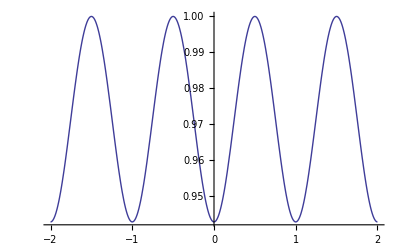

```mathematica
Plot[Sqrt[1-simpleCubicγk[{h,0,1}]^2],{h,-2,2}]
```

The standard long-wavelength result: for small |𝓀|, the frequency is J𝓈√(2z)|𝓀|:

```mathematica
Abs[Normal[Series[
(evs/.𝓀[i_]:>ϵ*𝓀[i]),
{ϵ,0,1}]]]//ComplexExpand//PowerExpand
```

{2 √3 j 𝓈 ϵ √(𝓀[𝓍]^2+𝓀[𝓎]^2+𝓀[𝓏]^2),2 √3 j 𝓈 ϵ √(𝓀[𝓍]^2+𝓀[𝓎]^2+𝓀[𝓏]^2)}

```mathematica
testHamF=Total[quadraticApprox[
-j*hpHeisenberg[testΓ]/.{θ[_]->Pi/2,ϕ[_]->0}/.Rule[x_,2]:>Rule[x,1]
]]
symplecticSpectrum0[FullSimplify[hamMatrix[
quadraticBosonFourier[testHamF,testΓ]
]]]
```

{-4 ⅈ j 𝓈 (-3+Cos[2 π 𝓀[1]]+Cos[2 π 𝓀[2]]+Cos[2 π 𝓀[3]]),4 ⅈ j 𝓈 (-3+Cos[2 π 𝓀[1]]+Cos[2 π 𝓀[2]]+Cos[2 π 𝓀[3]])}

## Definitions -- Spin-spin structure factor

incoherentCrossSection returns a list of the form {{ω_i, (I')_i}}, where the list is over all spin-wave branches, ω is the frequency of the branch at the given momentum 𝓆, and I(𝓆) is proportional to the scattering intensity (times the magnetic form factor for Fe2+ and a 𝓆-independent constant).

```mathematica
στVector[crystal_]:=
Module[
{basisPositions=SortBy[basisOffsets[crystal],First],
σcs,σas,τs},
τs=Exp[Factor[2Pi*I(#⟦2⟧.Array[τ,3])]]&/@basisPositions;
σcs=Coefficient[
Block[{gSpins=Quantum},
σ[#⟦1⟧]
],cr[b][Rule[0,#⟦1⟧]]]&/@basisPositions;
σas=Coefficient[
Block[{gSpins=Quantum},
σ[#⟦1⟧]
],an[b][Rule[0,#⟦1⟧]]]&/@basisPositions;
Return[
Refine[
Factor[(1/2)Join[
Reverse[directProduct[Conjugate[τs],σcs]],
directProduct[τs,σcs],
Reverse[directProduct[τs,σas]],
directProduct[Conjugate[τs],σas]
]],
Element[_,Reals]]
];
];
polarization[𝒬hat_]:=
Table[
KroneckerDelta[α,β]-𝒬hat[α]𝒬hat[β],
{α,3},{β,3}
];
makeSpinsFn[crystal_,couplingRules_,classicalSpinFn_]:=
Function[{Qhkl_List},
Evaluate[
Tr[
polarization[
N[Normalize[Qhkl.reciprocalBasisVectors[crystal]]]
].Transpose[
Outer[Times,#,#,2]&[
στVector[crystal]~replace~{
ϕRules,
couplingRules,
classicalSpinFn[couplingRules],
{τ[i_]:> toFirstBZ[crystal,Qhkl]⟦1,i⟧}
}],
{3,1,4,2}],
Plus,2]
]];
```

```mathematica
𝓃Boson[ω_,T_]:=1/(Exp[ℏ*ω/(𝓀B*T)]-1);
incoherentCrossSection[Qhkl_,T_,hamFn_,spinsFn_,crystal_]:=
Module[
{Qhat,tau,q,ωs,symp,ββ,
n=nBasis[crystal]},
Qhat=Normalize[Qhkl.reciprocalBasisVectors[crystal]];
{tau,q}=toFirstBZ[crystal,Qhkl];
{ωs,symp}=symplecticDiag[hamFn[Qhkl]];
ββ=(spinsFn[tau,Qhat]⊤symp);
Return[
Table[
(1+𝓃Boson[ωs⟦j⟧,T])*
(ββ⟦2n+j,j⟧+ββ⟦4n+1-j,2n+1-j⟧),
{j,n}]
]
];
```

### Iron atom magnetic form factor

Total orbital angular momentum on the Fe2+ should be completely quenched since complex is in a high spin state from the relatively small tetrahedral crystal field splitting. Assuming here that dominant contribution to L actually comes from the net spin via the spin-orbit coupling, resulting in an effective g>2. 
Reference:
Sections 5.1--5.3 of Marshall & Lovesey, Theory of thermal neutron scattering

fe2PlusJ encodes magnetic form factor coefficients for Fe2+, in the format {D,{{A,B,C},{a,b,c}}}.
Reference:
sec. 4.4.5 of International Tables for Crystallography, Volume C, 2006 edition
online at http://it.iucr.org/Cb/ch4o4v0001/sec4o4o5.pdf
same info available w/o institutional access at http://www.ill.eu/sites/ccsl/ffacts/ffachtml.html

```mathematica
fe2PlusJ[0]={-0.0119,{{0.0263,0.3668,0.6188},{34.9597,15.9435,5.5935}}};
fe2PlusJ[2]={0.0035,{{1.6490,1.9064,0.5206},{16.5593,6.1325,2.1370}}};
Clear[feFormFactor];
feFormFactor[g_,Nq_]:=With[
{s=Norm[Nq]/(4Pi)},
First[fe2PlusJ[0]]+Total[MapThread[#1*Exp[-#2*s^2]&,Last[fe2PlusJ[0]]]]+
(g-2)/g*s^2*
(First[fe2PlusJ[2]]+Total[MapThread[#1*Exp[-#2*s^2]&,Last[fe2PlusJ[2]]]])
];
```

## Problem-specific results -- classical:

## Lattices used in this calculation

```mathematica
ClearAll[𝔞tet,𝔠tet,tetragonalP];
dimension[tetragonalP]^=3;
unitBasisVectors[tetragonalP]^=IdentityMatrix[3];
latticeConstants[tetragonalP]^={𝔞tet,𝔞tet,𝔠tet};
N[𝔞tet]=8.1078;
N[𝔠tet]=5.1166;
bzFunction[tetragonalP]^=primitiveCellFn[reciprocalBasisVectors[tetragonalP],5];
```

```mathematica
feX=(1/2){1,1,0};
feY=(1/2){1,-1,0};
ClearAll[Γ2,Γ4];
bravaisLattice[Γ2]^=tetragonalP;
basisOffsets[Γ2]^={
{1}->{0,0,0},
{2}->feX
};
Γ2/:nearestNeighbors[Γ2,{1}]=
{{0,0,0}->{2},{-1,0,0}->{2},{0,-1,0}->{2},{-1,-1,0}->{2},(±{0,0,1})->{1}};
Γ2/:nearestNeighbors[Γ2,{2}]=
{{0,0,0}->{1},{1,0,0}->{1},{0,1,0}->{1},{1,1,0}->{1},(±{0,0,1})->{2}};
Γ4=supercell[Γ2,{1,1,2}];
```

```mathematica
Clear[sublatticeSign,sameSublatticeQ,samePlaneQ];
sublatticeSign[basis_List|Rule[_List,basis_List]]:=If[OddQ[First[basis]],1,-1];
sameSublatticeQ[site1_Rule,site2_Rule]:=
sublatticeSign[site1]==sublatticeSign[site2];
samePlaneQ[pos1_,pos2_]:=
(latticeℛ[gCrystal,pos1]⟦3⟧==latticeℛ[gCrystal,pos2]⟦3⟧);
```

Note: our convention is to always divide by # of sites in the unit cell (done in singleSiteOp and NNop below); this gives us the ground state energy per site, independent of the size of the cell.

```mathematica
sublatticeSign[{2,0,0,2}]
```

-1

## Classical MFT Hamiltonian

```mathematica
ϕMat=Inverse[(1/2)*{(1/2){1,1,1,1},2*{1,-1,-1,1},{-1,1,-1,1},{1,1,-1,-1}}];
ϕRules={θ[__]->0,ϕ[i_,0,0,j_]:>(ϕMat.{α+χ,β,γ+Φ+Pi,δ})⟦i+2j⟧};
```

```mathematica
spinSimp={θ[__]->0,ϕ[i_,0,0,j_]:>ϕ[2j+i]};
Block[{gCrystal=Γ4,gSpins=Classical},
mftEnergy=
(1/(𝓈(𝓈+1)ε2*Cos[Θ]))(
planarHeisenberg[{jxy,jz}]+
dz*dzyaloshinskiMoriya[]+
-gμB*zeeman[{hx,hy,0}]+
gsμB*anisotropicZ[{hx,hy,0}]+
Λ*easyPlane[]
)~replace~{spinSimp}
]
```

1/(𝓈 (1+𝓈) ε2)Sec[Θ] (1/4 gsμB (1+𝓈) (-hy Cos[ϕ[1]]+hy Cos[ϕ[2]]-hy Cos[ϕ[3]]+hy Cos[ϕ[4]]+hx Sin[ϕ[1]]-hx Sin[ϕ[2]]+hx Sin[ϕ[3]]-hx Sin[ϕ[4]])-1/4 gμB (1+𝓈) (hx Cos[ϕ[1]]+hx Cos[ϕ[2]]+hx Cos[ϕ[3]]+hx Cos[ϕ[4]]+hy Sin[ϕ[1]]+hy Sin[ϕ[2]]+hy Sin[ϕ[3]]+hy Sin[ϕ[4]])+1/8 dz 𝓈 (1+𝓈) (-8 Cos[ϕ[2]] Sin[ϕ[1]]+8 Cos[ϕ[1]] Sin[ϕ[2]]-8 Cos[ϕ[4]] Sin[ϕ[3]]+8 Cos[ϕ[3]] Sin[ϕ[4]])+1/8 𝓈 (1+𝓈) (8 jxy Cos[ϕ[1]] Cos[ϕ[2]]+2 jxy Cos[ϕ[1]] Cos[ϕ[3]]+2 jz Cos[ϕ[1]] Cos[ϕ[3]]+2 jxy Cos[ϕ[2]] Cos[ϕ[4]]+2 jz Cos[ϕ[2]] Cos[ϕ[4]]+8 jxy Cos[ϕ[3]] Cos[ϕ[4]]+8 jxy Sin[ϕ[1]] Sin[ϕ[2]]+2 jxy Sin[ϕ[1]] Sin[ϕ[3]]+2 jz Sin[ϕ[1]] Sin[ϕ[3]]+2 jxy Sin[ϕ[2]] Sin[ϕ[4]]+2 jz Sin[ϕ[2]] Sin[ϕ[4]]+8 jxy Sin[ϕ[3]] Sin[ϕ[4]]))

change to reduced parameters

change of angular variables and simplified definition of MFT energy in terms of these

```mathematica
Clear[modelE];
modelE[{𝒽_,tt_,ξ_},{α_,β_,γ_,δ_}]:=
-2Cos[β/2](Cos[γ]-tt*Cos[δ])-
2𝒽(Cos[α+β/4]Sin[(ξ-γ+δ)/2]+Cos[α-β/4]Sin[(ξ-γ-δ)/2]);
```

verify definition of modelE above:

```mathematica
reducedEnergy=
mftEnergy/(𝓈(𝓈+1)ε2*Cos[Θ])/.
reducedParams1/.reducedParams2//Simplify
testE=Collect[Total[reducedEnergy]/.ϕRules,tt|𝒽]//Simplify
TrigExpand[modelE[{𝒽,tt,ξ},{α,β,γ,δ}]-testE]
```

{2 Cos[1/2 (2 Φ+ϕ[1]-ϕ[2]+ϕ[3]-ϕ[4])] Cos[1/2 (ϕ[1]-ϕ[2]-ϕ[3]+ϕ[4])],tt (Cos[ϕ[1]-ϕ[3]]+Cos[ϕ[2]-ϕ[4]]),-𝒽 (Cos[1/2 (ξ+Φ-2 χ+2 ϕ[1])]+Cos[1/2 (ξ+Φ+2 χ-2 ϕ[2])]+Cos[1/2 (ξ+Φ-2 χ+2 ϕ[3])]+Cos[1/2 (ξ+Φ+2 χ-2 ϕ[4])]),0}

-Cos[1/2 (β-2 γ)]-Cos[β/2+γ]+tt Cos[1/2 (β-2 δ)]+tt Cos[β/2+δ]-𝒽 Sin[1/4 (4 α-β-2 (γ+δ-ξ))]+𝒽 Sin[1/4 (4 α-β+2 (γ+δ-ξ))]+𝒽 Sin[1/4 (4 α+β+2 γ-2 δ-2 ξ)]-𝒽 Sin[1/4 (4 α+β+2 (-γ+δ+ξ))]

0

## Definitions -- Change of variables (& couplings)

```mathematica
reducedParams1={
jxy->ε2*Cos[Φ]Cos[Θ],
jz->2*ε2*Sin[Θ],
dz->ε2*Sin[Φ]Cos[Θ],
gμB->ε1*Cos[ξ0],
gsμB->ε1*Sin[ξ0],
hx->h*Cos[χ],
hy->h*Sin[χ],
Λ->2ε2*Cos[Θ]*λ};
reducedParams2={
h->𝒽*𝓈(4ε2*Cos[Θ])/(ε1),
ξ0->(ξ+Φ)/2,
Tan[Θ]->tt};
```

```mathematica
ϕMat=Inverse[(1/2)*{(1/2){1,1,1,1},2*{1,-1,-1,1},{-1,1,-1,1},{1,1,-1,-1}}];
ϕRules={θ[__]->0,ϕ[i_,0,0,j_]:>(ϕMat.{α+χ,β,γ+Φ+Pi,δ})⟦i+2j⟧};
```

### Ground-state solution terms of original parameters

format for reduced model parameters = {{𝓈,𝒽,tt,ξ,Λr, ,Φ}
format for non-reduced model parameters = {s, {jxy, jz}, {g, gs}, {hx, hy}, Λ, dz}

```mathematica
With[{𝓈=p[[1]],jxy=p[[2,1]],jz=p[[2,2]],g=p[[3,1]],gs=p[[3,2]],hx=p[[4,1]],hy=p[[4,2]],Λ=p[[5]],dz=p[[6]]},
(*stuff goes here...*)
];
```

```mathematica
nRules[p_]:=With[
{ss=p[[1]],jxy=p[[2,1]],jz=p[[2,2]],g=p[[3,1]],gs=p[[3,2]],
hx=p[[4,1]],hy=p[[4,2]],Λ=p[[5]],dz=p[[6]]},
{𝓈->ss,
𝒽->μB/(4(ss+1))Sqrt[(hx^2+hy^2)(g^2+gs^2)/(jxy^2+dz^2)],
tt->jz/(2Sqrt[jxy^2+dz^2]),
ξ->ArcTan[g,gs]-ArcTan[jxy,dz]/2,
Φ->ArcTan[jxy,dz],
Λr->Λ/Sqrt[jxy^2+dz^2]
}];
verboseRules[inRules_]:=
nRules[Join[{#[[1]]},
Partition[#[[2;;5]],2],
#[[6;;8]]
]&[
First[Cases[inRules,Rule[#,x_]:>x]]&/@
{"Spin","In-plane J","Inter-plane J","g","Anisotropic g","External field vector","Easy-plane","D-M"}
]];
```

```mathematica
nSymplecticSpectrum[hpHamMatrix,
modelAFγδRules[𝒽,tt,ξ],
verboseRules[
{"Spin"->2,
"In-plane J"->0.3,
"Inter-plane J"->0.1,
"g"->2,
"Anisotropic g"->0,
"External field vector"->{5,0},
"Easy-plane"->0,
"D-M"->0
}],
{1,0,1/2}]
```

```mathematica
n𝒽[p_]:=With[
{𝓈=p[[1]],jxy=p[[2,1]],g=p[[3,1]],gs=p[[3,2]],
hx=p[[4,1]],hy=p[[4,2]],dz=p[[6]]},
μB/(4𝓈)Sqrt[(hx^2+hy^2)(g^2+gs^2)/(jxy^2+dz^2)]
];
nΦ[p_]:=With[
{jxy=p[[2,1]],dz=p[[6]]},
ArcTan[jxy,dz]
];
nTanΘ[p_]:=With[
{jxy=p[[2,1]],jz=p[[2,2]],dz=p[[6]]},
jz/(2Sqrt[jxy^2+dz^2])
];
nξ[p_]:=With[
{jxy=p[[2,1]],g=p[[3,1]],gs=p[[3,2]],dz=p[[6]]},
ArcTan[g,gs]-ArcTan[jxy,dz]/2
];
nΛr[p_]:=With[
{jxy=p[[2,1]],Λ=p[[5]],dz=p[[6]]},
Λ/Sqrt[jxy^2+dz^2];
];
```

Convert back to original spin variables

```mathematica
modelϕs[𝒽_,tt_,ξ_,χ_,Φ_]:=With[
{γδ=modelγδ[𝒽,tt,ξ]},
ϕMat.{χ,0,-γδ[[1]]-ξ-Φ/2,γδ[[2]]}
];
nϕs[p_]:=With[
{g=p[[3,1]],gs=p[[3,2]],hx=p[[4,1]],hy=p[[4,2]],
γδ=nγδ[p]},
ϕMat.{ArcTan[hx,hy],0,-γδ[[1]]-ArcTan[g,gs],γδ[[2]]}
];
```

Spin-dependent electric polarization, as given in Penc

```mathematica
polarizationVecs[ϕs_]:=
MapIndexed[
With[{sx=Cos[#1],sy=Sin[#1],sz=0,r=(sublatticeSign@@#2),
latticeκ=24(Pi/180)},
{-Cos[2r*latticeκ](sx*sz+sz*sx)-Sin[2r*latticeκ](sy*sz+sz*sy),
Cos[2r*latticeκ](sy*sz+sz*sy)-Sin[2r*latticeκ](sx*sz+sz*sx),
Cos[2r*latticeκ](sy^2-sx^2)-Sin[2r*latticeκ](sx*sy+sy*sx)}
]&,ϕs
];
stagggeredZPolarization[ϕs_]:=
Total[
MapIndexed[
-(sublatticeSign@@#2)Dot[#1,n𝓏]&,
polarizationVecs[ϕs]
]];
```

## Numeric solutions

```mathematica
e1m[𝒽_,tt_,ξ_]:=
{#1,{0.0,0.0,γ,δ}/.#2}&@@NMinimize[
{modelE[{𝒽,tt,ξ},{0,0,γ,δ}],
-Pi≤γ≤Pi&&-Pi/2≤δ≤3Pi/2},
{γ,δ}];
e1p[𝒽_,tt_,ξ_]:=
{#1,{N[Pi],0.0,γ,δ}/.#2}&@@NMinimize[
{modelE[{𝒽,tt,ξ},{Pi,0,γ,δ}],
-Pi≤γ≤Pi&&-Pi/2≤δ≤3Pi/2},
{γ,δ}];
e2am[𝒽_,tt_,ξ_]:=
{#1,{0.0,β,γ,0.0}/.#2}&@@NMinimize[
{modelE[{𝒽,tt,ξ},{0,β,γ,0}],
-Pi≤γ≤Pi&&-Pi<β≤Pi},
{β,γ}];
e2ap[𝒽_,tt_,ξ_]:=
{#1,{N[Pi],β,γ,0.0}/.#2}&@@NMinimize[
{modelE[{𝒽,tt,ξ},{Pi,β,γ,0}],
-Pi≤γ≤Pi&&-Pi<β≤Pi},
{β,γ}];
e2bm[𝒽_,tt_,ξ_]:=
{#1,{N[-Pi/2],β,γ,N[Pi]}/.#2}&@@NMinimize[
{modelE[{𝒽,tt,ξ},{-Pi/2,β,γ,Pi}],
-Pi≤γ≤Pi&&-Pi<β≤Pi},
{β,γ}];
e2bp[𝒽_,tt_,ξ_]:=
{#1,{N[Pi/2],β,γ,N[Pi]}/.#2}&@@NMinimize[
{modelE[{𝒽,tt,ξ},{Pi/2,β,γ,Pi}],
-Pi≤γ≤Pi&&-Pi<β≤Pi},
{β,γ}];
e3[𝒽_,tt_,ξ_]:=
{#1,{α,0.0,γ,0.0}/.#2}&@@NMinimize[
{modelE[{𝒽,tt,ξ},{α,0,γ,0}],
-Pi≤γ≤Pi&&-Pi<α≤Pi},
{α,γ}];
eAll[𝒽_,tt_,ξ_]:=
First[SortBy[
Through[{e1m,e1p,e2am,e2ap,e2bm,e2bp,e3}[𝒽,tt,ξ]],
First]];
eFull[𝒽_,tt_,ξ_]:=
{#1,{α,β,γ,δ}/.#2}&@@NMinimize[
{modelE[{𝒽,tt,ξ},{α,β,γ,δ}],
-Pi≤α≤Pi&&-Pi≤β≤Pi&&-Pi≤γ≤Pi&&-Pi/2≤δ≤3Pi/2},
{α,β,γ,δ}];
```

```mathematica
nMinE[𝒽_,tt_,ξ_]:=
Min[
Through[{e1m,e1p,e2am,e2ap,e2bm,e2bp,e3}[𝒽,tt,ξ]][[All,1]]
];
nMinEPhase[𝒽_,tt_,ξ_]:=
Ordering[
Through[{e1m,e1p,e2am,e2ap,e2bm,e2bp,e3}[𝒽,tt,ξ]],
1,First[#1]<First[#2]&][[1]];
nMinESpins[𝒽_,tt_,ξ_]:=
SortBy[
Through[{e1m,e1p,e2am,e2ap,e2bm,e2bp,e3}[𝒽,tt,ξ]],
First][[1,2]];
nMinERealSpins[𝒽_,tt_,ξ_,Φ_,χ_]:=
ϕMat.({χ,0,Φ+Pi,0}+nMinESpins[𝒽,tt,ξ]);
```

```mathematica
dumbColors[i_]:=
Piecewise[
{{Lighter[Red],1/2<i<3/2},
{Darker[Red],3/2<i<5/2},
{Lighter[Blue],5/2<i<7/2},
{Darker[Blue],7/2<i<9/2},
{Lighter[Green],9/2<i<11/2},
{Darker[Green],11/2<i<13/2},
{Darker[Yellow],13/2<i<15/2}},
White
];
```

```mathematica
Prepend[2,zfBestFit[[2,All,2]]]
```

Prepend::normal: Nonatomic expression expected at position 1 in Prepend[2, {0.0869998, 0.11731, 0.456446, 0.368563}].

Prepend[2,{0.0869998,0.11731,0.456446,0.368563}]

```mathematica
foo2=
ParallelTable[
{zfRealField[h,{2,ε2_,Θ_,Φ_,λ_},
{2.1,0.3}],xi/Pi,
Last[nMinESpins[h,0.36,xi]]/Pi},
{h,0.01,1.0,0.05},
{xi,-3/4Pi,3/4Pi,0.25}
];
```

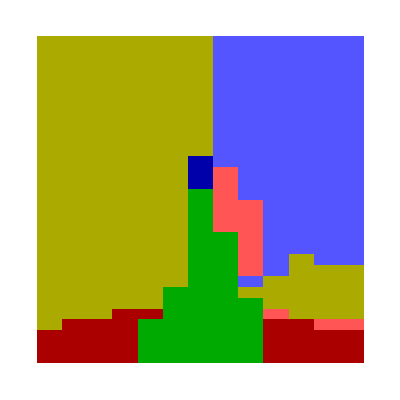

```mathematica
ArrayPlot[foo,
AspectRatio->1,
ColorFunction->dumbColors,
ColorFunctionScaling->False,
DataReversed->True,
DataRange->{{-1/2,1/2},{0,3}},
FrameTicks->{Range[0,3,0.25],Range[-1/2,1/2,1/8]},
FrameLabel->{"h","ξ/π"}]
```

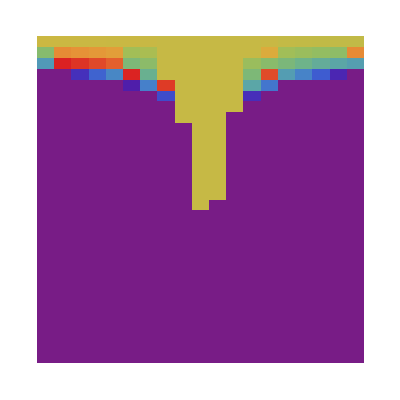

```mathematica
ArrayPlot[foo2,
AspectRatio->1,
ColorFunction->"Rainbow",
ColorFunctionScaling->True,
DataRange->{{-3/4,3/4},{0,3}},
FrameTicks->{Range[0,3.0,0.25],Range[-3/4,3/4,1/4]},
FrameLabel->{"h","ξ/π"}]
```

```mathematica
foo2=
ParallelTable[
Last[nMinESpins[h,0.135,xi]]/Pi,
{h,0.01,2.5,0.1},
{xi,-1/4Pi,1/4Pi,0.075}
];
```

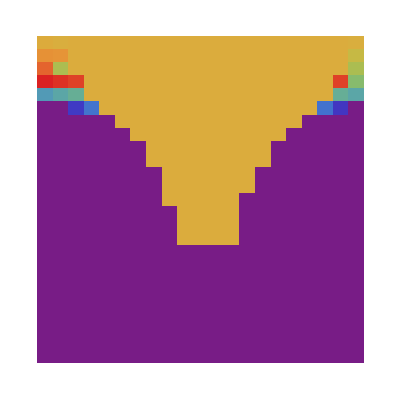

```mathematica
ArrayPlot[foo2,
AspectRatio->1,
ColorFunction->"Rainbow",
ColorFunctionScaling->True,
DataRange->{{-1/4,1/4},{0,2.5}},
FrameTicks->{Range[0,2.5,0.25],Range[-1/4,1/4,1/8]},
FrameLabel->{"h","ξ/π"}]
```

```mathematica
Min[foo2]
Max[foo2]
```

-3.4265×10^-8

1.34369

```mathematica
Pi/16//N
```

0.19635

```mathematica
4*Cos[ArcTan[0.1045]]/μB*1.5/6.5
```

15.8607

```mathematica
foo3=
ParallelTable[
{h,nMinESpins[h,0.135,0.0]},
{h,0.01,20.0,0.2}];
```

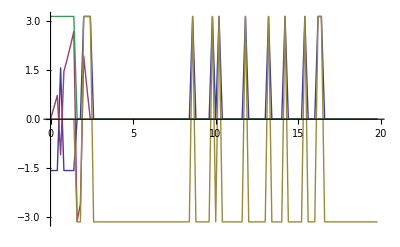

```mathematica
ListPlot[Transpose[Thread/@foo3],Joined->True]
```

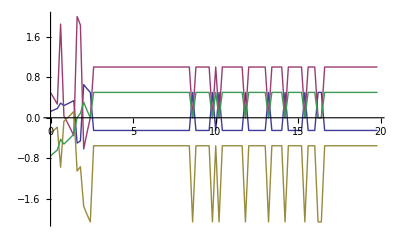

```mathematica
ListPlot[Transpose[Thread/@({#[[1]],(Inverse[ϕMat].#[[2]]-{0,0,Pi+0.162,0})/Pi}&/@foo3)],Joined->True]
```

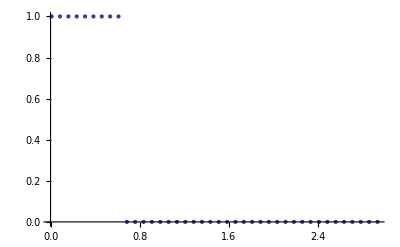

```mathematica
ListPlot[foo3]
```

## Results from analytic solution (I)

### Ground-state solution terms of reduced parameters

Critical external field for AF-F transition -- if only one real root, that’s the answer, otherwise pick the middle one

```mathematica
𝒽c[tt_,ξ_]:=Module[{c=Cos[2ξ],sols},
sols=Sort[Select[
Table[
N[Root[#1^3-#1^2(4tt^2+8tt*c+1-c^2)+16tt^2*#1*(1+2c*tt)-64tt^4&,k]],
{k,3}],
Element[#,Reals]&
]];
If[
Length[sols]==1,Sqrt[sols[[1]]],Sqrt[sols[[2]]]
]
];
```

Classical GS energy in the AF, F phases

```mathematica
afEnergy[𝒽_,tt_,ξ_]:=With[{x=𝒽^2/(4tt)},
-tt-x-Sqrt[1+x^2-2x*Cos[2ξ]]
];
fEnergy[𝒽_,tt_,ξ_]:=With[{z=𝒽^2/2*Cos[2ξ],y=𝒽^2-1},
Min[Select[Table[
N[Root[
#1^4-6 #1^3* z+(#1^2 /4)(-27-18 y+y^2+48 z^2)-#1*z (-9 y+y^2+8 z^2)+y^2 (-y+z^2)&,k]],
{k,4}],Element[#,Reals]&]
]+tt-𝒽^2*Cos[2ξ]];
modelGS::energy="Incorrectly predicted `2` phase at reduced parameters `1`.";
modelEnergy[𝒽_,tt_,ξ_]:=With[
{hc=𝒽c[tt,ξ],fE=fEnergy[𝒽,tt,ξ],afE=afEnergy[𝒽,tt,ξ]},
Which[
𝒽<hc&&fE≥afE,afE,
𝒽>hc&&fE≤afE,fE,
𝒽<hc&&fE<afE,Message[modelGS::energy,{𝒽,tt,ξ},"AF"];fE,
True,Message[modelGS::energy,{𝒽,tt,ξ},"F"];afE
]];
```

GS spin configuration variables in the AF, F phases. Include error check that γ,δ is an extremum for the given parameters.

```mathematica
afγ[𝒽_,tt_,ξ_]:=With[{x=𝒽^2/(4tt)},
-(1/2)ArcTan[Cos[2ξ]-x,Sin[2ξ]]+Pi/2
];
afδ[𝒽_,tt_,ξ_]:=With[{x=𝒽^2/(4tt)},
Re[ArcCos[𝒽/(2tt)*Sqrt[
(1/2)(1-(Cos[2ξ]-x)/Sqrt[1+x^2-2x*Cos[2ξ]])
]
]]];
modelAFγδRules[𝒽_,tt_,ξ_]:=
MapThread[Rule,{{γ,δ},{afγ[𝒽,tt,ξ],afδ[𝒽,tt,ξ]}}];
fγ[𝒽_,tt_,ξ_]:=
2ArcTan[
Min[Select[
Table[
N[Root[
Sin[2ξ](#1^4-6#1^2+1)-
4Cos[2ξ](#1^3-#1)-
2𝒽(#1^3+#1)&,k]],
{k,4}],
Element[#,Reals]&&0≤2ArcTan[#]≤Pi&]
]];
modelFγδRules[𝒽_,tt_,ξ_]:=
MapThread[Rule,{{γ,δ},{fγ[𝒽,tt,ξ],0}}];
modelγδ[𝒽_,tt_,ξ_]:=
modelGStest1[If[
𝒽<𝒽c[tt,ξ],
{afγ[𝒽,tt,ξ],afδ[𝒽,tt,ξ]},
{fγ[𝒽,tt,ξ],0}
],𝒽,tt,ξ];
modelγδRules[𝒽_,tt_,ξ_]:=
MapThread[Rule,{{γ,δ},modelγδ[𝒽,tt,ξ]}];
```

### Ground-state solution terms of original parameters

```mathematica
modelϕs[𝒽_,tt_,ξ_,χ_,Φ_]:=With[
{γδ=modelγδ[𝒽,tt,ξ]},
ϕMat.{χ,0,-γδ[[1]]-ξ-Φ/2,γδ[[2]]}
];
n𝒽c[p_]:=𝒽c[nTanΘ[p],nξ[p]];
nHc[p_]:=With[
{𝓈=p[[1]],jxy=p[[2,1]],g=p[[3,1]],gs=p[[3,2]],dz=p[[6]]},
4(𝓈+1)𝒽c[nTanΘ[p],nξ[p]]/μB*Sqrt[(jxy^2+dz^2)/(g^2+gs^2)]
];
nEnergy[p_]:=modelEnergy[n𝒽[p],nTanΘ[p],nξ[p]];
nγδ[p_]:=With[
{𝒽=n𝒽[p],tt=nTanΘ[p],ξ=nξ[p],Λr=nΛr[p],Φ=nΦ[p]},
modelGStest2[If[
𝒽<n𝒽c[p],
{afγ[𝒽,tt,ξ],afδ[𝒽,tt,ξ]},
{fγ[𝒽,tt,ξ],0}
],𝒽,tt,ξ,Λr,Φ]
];
nγδRules[p_]:=
MapThread[Rule,{{γ,δ},nγδ[p]}];
```

## Problem-specific results -- quantum:

## Quantum MFT Hamiltonian

```mathematica
flavorsNCQ[op1_,op2_]:=Last[Last[op1]]==Last[Last[op2]];

hamCleanup[expn_]:=
Collect[
ExpToTrig[TrigReduce[expn]]/.(b:boson)[x_]:>b[Expand[x]],
𝒽|𝓈|tt,
TrigFactor
];
makeHamiltonian0[expn_,crystal_]:=
Module[{step2,step3},
step2=operatorTruncate[expn,2];
step3=Plus@@@quadraticBosonSym[Last[step2],flavorsNCQ];
hamCleanup[{
First[step2]+First[step3],
step2[[2]],
quadraticBosonFourier[Last[step3],crystal]
}]
];
```

```mathematica
Join[First[Solve[γq==latticeγ[crystal,1], Cos[π 𝓆[1]]]],
{Sin[x_]^(n_Integer):>(1-Cos[x]^2)^(n/2)/;EvenQ[n]}]
```

In terms of reduced couplings defined above:

```mathematica
makeHamiltonian[terms_,rules_,orignalCrystal_,dupes_]:=
Module[
{step1,step2,step3},
step1=operatorTruncate[
supercell[#/.rules,dupes],
2]&/@(terms);
step2=Plus@@@Expand[
1/(ε2*Cos[Θ])Transpose[step1]/.reducedParams1
]/.reducedParams2;
step3=Plus@@@quadraticBosonSym[Last[step2],flavorsNCQ];
hamCleanup[{
First[step2]+First[step3],
step2[[2]],
quadraticBosonFourier[Last[step3],orignalCrystal]
}]
];
```

```mathematica
quadratic𝓆CoeffsHam[expn_]:=
ArrayFlatten[{
{{{#1}},{#2}},
{0,#3}
}]&@@
Most[CoefficientArrays[
TrigExpand[expn]+Cos[Pi*𝓆[1]]^3/.Sin[x_]^2:>1-Cos[x]^2,
Table[Cos[π 𝓆[i]],{i,3}]
]//Normal];
bosonsToHamCoeffs[ham_]:=
Transpose[
Map[quadratic𝓆CoeffsHam,(ε2*Cos[ArcTan[tt]])quadraticCoeffs[ham],{2}],
{2,3,1,4}];
evaluateHam[𝓆_,hamCoeffs_]:=
(#.hamCoeffs.#)&[
Join[{1},Cos[Pi*𝓆]]
]
```

```mathematica
{hpHam0,hpHam1,hpHam2}=
makeHamiltonian[{
hpPlanarHeisenberg[{jxy,jz},Γ4],
dz*hpDzyaloshinskiMoriya[Γ4],
-gμB*hpZeeman[{hx,hy,0},Γ4],
gsμB*hpAnisotropicZ[{hx,hy,0},Γ4],
Λ*hpEasyPlane[Γ4]
},
ϕRules,Γ2,{1,1,2}];
hpHamCoeffs=hamCleanup[bosonsToHamCoeffs[hpHam2]];
```

```mathematica
hpHam0//Simplify
```

1/4 𝓈 (-(1+𝓈) Cos[β/2] (8 Cos[γ]-2 Cos[δ] (2 tt+Cos[Φ]))+2 𝒽 (1+2 𝓈) (-Sin[1/4 (4 α-β-2 (γ+δ-ξ))]+Sin[1/4 (4 α-β+2 (γ+δ-ξ))]+2 Cos[α+β/4] Sin[1/2 (γ-δ-ξ)]))

The reuqirement that terms linear in boson operators vanish is equivalent to the requirement that the variables {α,β,γ.δ} describe an extremum of the classical Hamiltonian:

```mathematica
Sqrt[2]/(𝓈*Sqrt[𝓈])*linearCoeffs[hpHam1]//Simplify//TableForm
```

1/4 ⅈ (4 𝒽 Cos[1/4 (4 α+β+2 (-γ+δ+ξ))]-4 Sin[1/2 (β-2 γ)]+(2 tt+Cos[Φ]) Sin[β/2+δ])
1/8 ⅈ (8 𝒽 Cos[1/4 (4 α-β-2 (γ+δ-ξ))]+8 Sin[β/2+γ]-2 (2 tt+Cos[Φ]) Sin[β/2+δ])
-1/4 ⅈ (4 𝒽 Cos[1/4 (4 α-β+2 (γ+δ-ξ))]-4 Sin[1/2 (β-2 γ)]+(2 tt+Cos[Φ]) Sin[1/2 (β-2 δ)])
-1/8 ⅈ (8 𝒽 Cos[1/4 (4 α+β+2 γ-2 δ-2 ξ)]+8 Sin[β/2+γ]-2 (2 tt+Cos[Φ]) Sin[1/2 (β-2 δ)])
-1/4 ⅈ (4 𝒽 Cos[1/4 (4 α+β+2 (-γ+δ+ξ))]-4 Sin[1/2 (β-2 γ)]+(2 tt+Cos[Φ]) Sin[β/2+δ])
-1/8 ⅈ (8 𝒽 Cos[1/4 (4 α-β-2 (γ+δ-ξ))]+8 Sin[β/2+γ]-2 (2 tt+Cos[Φ]) Sin[β/2+δ])
1/4 ⅈ (4 𝒽 Cos[1/4 (4 α-β+2 (γ+δ-ξ))]-4 Sin[1/2 (β-2 γ)]+(2 tt+Cos[Φ]) Sin[1/2 (β-2 δ)])
1/8 ⅈ (8 𝒽 Cos[1/4 (4 α+β+2 γ-2 δ-2 ξ)]+8 Sin[β/2+γ]-2 (2 tt+Cos[Φ]) Sin[1/2 (β-2 δ)])

## Quantum MFT Hamiltonian, revised

```mathematica
reducedParams1={
jxy->ε2*Cos[Φ]Cos[Θ],
jz->2*ε2*Sin[Θ],
dz->ε2*Sin[Φ]Cos[Θ],
gμB->ε1*Cos[ξ0],
gsμB->ε1*Sin[ξ0],
hx->h*Cos[χ],
hy->h*Sin[χ],
Λ->2ε2*Cos[Θ]*λ};
reducedParams2={
h->𝒽*𝓈(4ε2*Cos[Θ])/(ε1),
ξ0->(ξ+Φ)/2,
Tan[Θ]->tt};
```

```mathematica
spinSimp={θ[__]->0,ϕ[i_,0,0,j_]:>ϕ[2j+i]};
```

```mathematica
ϕMat=Inverse[(1/2)*{(1/2){1,1,1,1},2*{1,-1,-1,1},{-1,1,-1,1},{1,1,-1,-1}}];
ϕRules={θ[__]->0,ϕ[i_,0,0,j_]:>(ϕMat.{α+χ,β,γ+Φ+Pi,δ})⟦i+2j⟧};
```

```mathematica
Clear[hamMat];
Block[{gCrystal=Γ4,gSpins=Quantum},
step1=operatorTruncate[
(1/(𝓈*ε2*Cos[Θ]))(
planarHeisenberg[{jxy,jz}]+
dz*dzyaloshinskiMoriya[]+
-gμB*zeeman[{hx,hy,0}]+
gsμB*anisotropicZ[{hx,hy,0}]+
Λ*easyPlane[])~replace~{ϕRules,reducedParams1,reducedParams2},
2];
step2=Plus@@@quadraticBosonSym[Last[step1]];
hamm=hamCleanup[{
First[step1]+First[step2],
step1[[2]],
quadraticBosonFourier[Last[step2],Array[qq,3]]
}];
hamMat=Collect[
TrigExpand[
quadraticCoeffs[hamm[[3]]]
]/.Tan[Θ]->tt,
tt|𝒽,TrigReduce];
];
```

```mathematica
First[hamm]//Simplify
```

1/(2 (1+𝓈))(𝒽 (1+2 𝓈) (-Sin[1/4 (4 α-β-2 (γ+δ-ξ))]+Sin[1/4 (4 α-β+2 (γ+δ-ξ))]+2 Cos[α+β/4] Sin[1/2 (γ-δ-ξ)])-4 (1+𝓈) Cos[β/2] (Cos[γ]-Cos[δ] Tan[Θ]))

```mathematica
Block[{gCrystal=Γ4,gSpins=Quantum},
minEqns=Collect[
TrigExpand[
(8(𝓈+1)Sqrt[2])/(I*Sqrt[𝓈])*linearCoeffs[hamm[[2]]]
]⟦1,1;;4⟧/.Tan[Θ]->tt,
tt|𝒽,TrigFactor]
]//TableForm
```

8 𝒽 Cos[α+β/4-γ/2+δ/2+ξ/2]-16 Cos[β/4-γ/2] Sin[β/4-γ/2]+16 tt Cos[β/4+δ/2] Sin[β/4+δ/2]
8 𝒽 Cos[α-β/4-γ/2-δ/2+ξ/2]+16 Cos[β/4+γ/2] Sin[β/4+γ/2]-16 tt Cos[β/4+δ/2] Sin[β/4+δ/2]
-8 𝒽 Cos[α-β/4+γ/2+δ/2-ξ/2]+16 Cos[β/4-γ/2] Sin[β/4-γ/2]-16 tt Cos[β/4-δ/2] Sin[β/4-δ/2]
-8 𝒽 Cos[α+β/4+γ/2-δ/2-ξ/2]-16 Cos[β/4+γ/2] Sin[β/4+γ/2]+16 tt Cos[β/4-δ/2] Sin[β/4-δ/2]

```mathematica
nMinESpins[0.5,0.3,0.0]
```

{-1.5708,0.774053,-7.53071×10^-9,3.14159}

```mathematica
Thread[Rule[{α,β,γ,δ},nMinESpins[0.5,0.3,0.0]]]
```

{α→-1.5708,β→0.774053,γ→-7.53071×10^-9,δ→3.14159}

```mathematica
TrigExpand[minEqns]~replace~{{𝒽->0.5,tt->0.3,ξ->0},
Thread[Rule[{α,β,γ,δ},nMinESpins[0.5,0.3,0.0]]]}
```

{-3.01767×10^-8,-8.71954×10^-8,3.01767×10^-8,8.71954×10^-8}

### ok, lock&load

```mathematica
testCouplings={𝓈->2,χ->Pi/2,𝒽->0.8,tt->0.3,ξ->-0.1,λ->1.0,Φ->0.15*Pi};
```

```mathematica
ghettoSpinFn[couplingRules_]:=
Thread[
Rule[{α,β,γ,δ},nMinESpins@@({𝒽,tt,ξ}/.couplingRules)]
];
```

```mathematica
ghettoSpinFn[testCouplings]
```

{α→1.5708,β→-1.24993,γ→-0.0131633,δ→3.14159}

```mathematica
hamMat//Dimensions
```

{16,16}

```mathematica
makeHamFn0[hamMatrix_,couplingRules_,classicalSpinFn_]:=
Function[{qH,qK,qL},
Evaluate[
ArrayFlatten[{
{{{#1}},{#2}},
{0,#3}
}]&@@
Most[CoefficientArrays[
TrigExpand[
(hamMatrix/.(f:Cos|Sin)[x_]:>f[Expand[x]])
]+Cos[Pi*qH]^3/.Sin[x_]^2:>1-Cos[x]^2,
Table[Cos[Pi*QQ[j]],{j,3}]
]//Normal]
]

];
```

```mathematica
TrigExpand[(hamMat/.{(f:Cos|Sin)[x_]:>f[Expand[x]]})]
```

{{0,0,0,0,0,1/2 Cos[β/2] Cos[γ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[Φ] Cos[π QQQ[1]] Cos[π QQQ[2]]-1/2 Cos[π QQQ[1]] Cos[π QQQ[2]] Sin[β/2] Sin[γ],1/2 tt Cos[π QQQ[3]]-1/2 tt Cos[β/2] Cos[δ] Cos[π QQQ[3]]-1/2 tt Cos[π QQQ[3]] Sin[β/2] Sin[δ],λ/2,λ/2+Cos[β/4]^2 Cos[γ/2]^2-tt Cos[β/4]^2 Cos[δ/2]^2-𝒽 Cos[β/4] Cos[γ/2] Cos[δ/2] Cos[ξ/2] Sin[α]-𝒽 Cos[α] Cos[γ/2] Cos[δ/2] Cos[ξ/2] Sin[β/4]-Cos[γ/2]^2 Sin[β/4]^2+tt Cos[δ/2]^2 Sin[β/4]^2-𝒽 Cos[α] Cos[β/4] Cos[δ/2] Cos[ξ/2] Sin[γ/2]-4 Cos[β/4] Cos[γ/2] Sin[β/4] Sin[γ/2]+𝒽 Cos[δ/2] Cos[ξ/2] Sin[α] Sin[β/4] Sin[γ/2]-Cos[β/4]^2 Sin[γ/2]^2+Sin[β/4]^2 Sin[γ/2]^2+𝒽 Cos[α] Cos[β/4] Cos[γ/2] Cos[ξ/2] Sin[δ/2]-4 tt Cos[β/4] Cos[δ/2] Sin[β/4] Sin[δ/2]-𝒽 Cos[γ/2] Cos[ξ/2] Sin[α] Sin[β/4] Sin[δ/2]-𝒽 Cos[β/4] Cos[ξ/2] Sin[α] Sin[γ/2] Sin[δ/2]-𝒽 Cos[α] Cos[ξ/2] Sin[β/4] Sin[γ/2] Sin[δ/2]+tt Cos[β/4]^2 Sin[δ/2]^2-tt Sin[β/4]^2 Sin[δ/2]^2+𝒽 Cos[α] Cos[β/4] Cos[γ/2] Cos[δ/2] Sin[ξ/2]-𝒽 Cos[γ/2] Cos[δ/2] Sin[α] Sin[β/4] Sin[ξ/2]-𝒽 Cos[β/4] Cos[δ/2] Sin[α] Sin[γ/2] Sin[ξ/2]-𝒽 Cos[α] Cos[δ/2] Sin[β/4] Sin[γ/2] Sin[ξ/2]+𝒽 Cos[β/4] Cos[γ/2] Sin[α] Sin[δ/2] Sin[ξ/2]+𝒽 Cos[α] Cos[γ/2] Sin[β/4] Sin[δ/2] Sin[ξ/2]+𝒽 Cos[α] Cos[β/4] Sin[γ/2] Sin[δ/2] Sin[ξ/2]-𝒽 Sin[α] Sin[β/4] Sin[γ/2] Sin[δ/2] Sin[ξ/2],1/2 tt Cos[π QQQ[3]]+1/2 tt Cos[β/2] Cos[δ] Cos[π QQQ[3]]+1/2 tt Cos[π QQQ[3]] Sin[β/2] Sin[δ],-1/2 Cos[β/2] Cos[γ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[Φ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[π QQQ[1]] Cos[π QQQ[2]] Sin[β/2] Sin[γ],0,0,0,0,0},{0,0,0,0,1/2 Cos[β/2] Cos[γ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[Φ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[π QQQ[1]] Cos[π QQQ[2]] Sin[β/2] Sin[γ],0,λ/2,1/2 tt Cos[π QQQ[3]]-1/2 tt Cos[β/2] Cos[δ] Cos[π QQQ[3]]-1/2 tt Cos[π QQQ[3]] Sin[β/2] Sin[δ],1/2 tt Cos[π QQQ[3]]+1/2 tt Cos[β/2] Cos[δ] Cos[π QQQ[3]]+1/2 tt Cos[π QQQ[3]] Sin[β/2] Sin[δ],λ/2+Cos[β/4]^2 Cos[γ/2]^2-tt Cos[β/4]^2 Cos[δ/2]^2-𝒽 Cos[β/4] Cos[γ/2] Cos[δ/2] Cos[ξ/2] Sin[α]+𝒽 Cos[α] Cos[γ/2] Cos[δ/2] Cos[ξ/2] Sin[β/4]-Cos[γ/2]^2 Sin[β/4]^2+tt Cos[δ/2]^2 Sin[β/4]^2-𝒽 Cos[α] Cos[β/4] Cos[δ/2] Cos[ξ/2] Sin[γ/2]+4 Cos[β/4] Cos[γ/2] Sin[β/4] Sin[γ/2]-𝒽 Cos[δ/2] Cos[ξ/2] Sin[α] Sin[β/4] Sin[γ/2]-Cos[β/4]^2 Sin[γ/2]^2+Sin[β/4]^2 Sin[γ/2]^2-𝒽 Cos[α] Cos[β/4] Cos[γ/2] Cos[ξ/2] Sin[δ/2]-4 tt Cos[β/4] Cos[δ/2] Sin[β/4] Sin[δ/2]-𝒽 Cos[γ/2] Cos[ξ/2] Sin[α] Sin[β/4] Sin[δ/2]+𝒽 Cos[β/4] Cos[ξ/2] Sin[α] Sin[γ/2] Sin[δ/2]-𝒽 Cos[α] Cos[ξ/2] Sin[β/4] Sin[γ/2] Sin[δ/2]+tt Cos[β/4]^2 Sin[δ/2]^2-tt Sin[β/4]^2 Sin[δ/2]^2+𝒽 Cos[α] Cos[β/4] Cos[γ/2] Cos[δ/2] Sin[ξ/2]+𝒽 Cos[γ/2] Cos[δ/2] Sin[α] Sin[β/4] Sin[ξ/2]-𝒽 Cos[β/4] Cos[δ/2] Sin[α] Sin[γ/2] Sin[ξ/2]+𝒽 Cos[α] Cos[δ/2] Sin[β/4] Sin[γ/2] Sin[ξ/2]-𝒽 Cos[β/4] Cos[γ/2] Sin[α] Sin[δ/2] Sin[ξ/2]+𝒽 Cos[α] Cos[γ/2] Sin[β/4] Sin[δ/2] Sin[ξ/2]-𝒽 Cos[α] Cos[β/4] Sin[γ/2] Sin[δ/2] Sin[ξ/2]-𝒽 Sin[α] Sin[β/4] Sin[γ/2] Sin[δ/2] Sin[ξ/2],0,-1/2 Cos[β/2] Cos[γ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[Φ] Cos[π QQQ[1]] Cos[π QQQ[2]]-1/2 Cos[π QQQ[1]] Cos[π QQQ[2]] Sin[β/2] Sin[γ],0,0,0,0},{0,0,0,0,1/2 tt Cos[π QQQ[3]]-1/2 tt Cos[β/2] Cos[δ] Cos[π QQQ[3]]+1/2 tt Cos[π QQQ[3]] Sin[β/2] Sin[δ],λ/2,0,1/2 Cos[β/2] Cos[γ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[Φ] Cos[π QQQ[1]] Cos[π QQQ[2]]-1/2 Cos[π QQQ[1]] Cos[π QQQ[2]] Sin[β/2] Sin[γ],-1/2 Cos[β/2] Cos[γ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[Φ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[π QQQ[1]] Cos[π QQQ[2]] Sin[β/2] Sin[γ],0,λ/2+Cos[β/4]^2 Cos[γ/2]^2-tt Cos[β/4]^2 Cos[δ/2]^2+𝒽 Cos[β/4] Cos[γ/2] Cos[δ/2] Cos[ξ/2] Sin[α]-𝒽 Cos[α] Cos[γ/2] Cos[δ/2] Cos[ξ/2] Sin[β/4]-Cos[γ/2]^2 Sin[β/4]^2+tt Cos[δ/2]^2 Sin[β/4]^2-𝒽 Cos[α] Cos[β/4] Cos[δ/2] Cos[ξ/2] Sin[γ/2]-4 Cos[β/4] Cos[γ/2] Sin[β/4] Sin[γ/2]-𝒽 Cos[δ/2] Cos[ξ/2] Sin[α] Sin[β/4] Sin[γ/2]-Cos[β/4]^2 Sin[γ/2]^2+Sin[β/4]^2 Sin[γ/2]^2-𝒽 Cos[α] Cos[β/4] Cos[γ/2] Cos[ξ/2] Sin[δ/2]+4 tt Cos[β/4] Cos[δ/2] Sin[β/4] Sin[δ/2]-𝒽 Cos[γ/2] Cos[ξ/2] Sin[α] Sin[β/4] Sin[δ/2]-𝒽 Cos[β/4] Cos[ξ/2] Sin[α] Sin[γ/2] Sin[δ/2]+𝒽 Cos[α] Cos[ξ/2] Sin[β/4] Sin[γ/2] Sin[δ/2]+tt Cos[β/4]^2 Sin[δ/2]^2-tt Sin[β/4]^2 Sin[δ/2]^2+𝒽 Cos[α] Cos[β/4] Cos[γ/2] Cos[δ/2] Sin[ξ/2]+𝒽 Cos[γ/2] Cos[δ/2] Sin[α] Sin[β/4] Sin[ξ/2]+𝒽 Cos[β/4] Cos[δ/2] Sin[α] Sin[γ/2] Sin[ξ/2]-𝒽 Cos[α] Cos[δ/2] Sin[β/4] Sin[γ/2] Sin[ξ/2]+𝒽 Cos[β/4] Cos[γ/2] Sin[α] Sin[δ/2] Sin[ξ/2]-𝒽 Cos[α] Cos[γ/2] Sin[β/4] Sin[δ/2] Sin[ξ/2]-𝒽 Cos[α] Cos[β/4] Sin[γ/2] Sin[δ/2] Sin[ξ/2]-𝒽 Sin[α] Sin[β/4] Sin[γ/2] Sin[δ/2] Sin[ξ/2],1/2 tt Cos[π QQQ[3]]+1/2 tt Cos[β/2] Cos[δ] Cos[π QQQ[3]]-1/2 tt Cos[π QQQ[3]] Sin[β/2] Sin[δ],0,0,0,0},{0,0,0,0,λ/2,1/2 tt Cos[π QQQ[3]]-1/2 tt Cos[β/2] Cos[δ] Cos[π QQQ[3]]+1/2 tt Cos[π QQQ[3]] Sin[β/2] Sin[δ],1/2 Cos[β/2] Cos[γ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[Φ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[π QQQ[1]] Cos[π QQQ[2]] Sin[β/2] Sin[γ],0,0,-1/2 Cos[β/2] Cos[γ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[Φ] Cos[π QQQ[1]] Cos[π QQQ[2]]-1/2 Cos[π QQQ[1]] Cos[π QQQ[2]] Sin[β/2] Sin[γ],1/2 tt Cos[π QQQ[3]]+1/2 tt Cos[β/2] Cos[δ] Cos[π QQQ[3]]-1/2 tt Cos[π QQQ[3]] Sin[β/2] Sin[δ],λ/2+Cos[β/4]^2 Cos[γ/2]^2-tt Cos[β/4]^2 Cos[δ/2]^2+𝒽 Cos[β/4] Cos[γ/2] Cos[δ/2] Cos[ξ/2] Sin[α]+𝒽 Cos[α] Cos[γ/2] Cos[δ/2] Cos[ξ/2] Sin[β/4]-Cos[γ/2]^2 Sin[β/4]^2+tt Cos[δ/2]^2 Sin[β/4]^2-𝒽 Cos[α] Cos[β/4] Cos[δ/2] Cos[ξ/2] Sin[γ/2]+4 Cos[β/4] Cos[γ/2] Sin[β/4] Sin[γ/2]+𝒽 Cos[δ/2] Cos[ξ/2] Sin[α] Sin[β/4] Sin[γ/2]-Cos[β/4]^2 Sin[γ/2]^2+Sin[β/4]^2 Sin[γ/2]^2+𝒽 Cos[α] Cos[β/4] Cos[γ/2] Cos[ξ/2] Sin[δ/2]+4 tt Cos[β/4] Cos[δ/2] Sin[β/4] Sin[δ/2]-𝒽 Cos[γ/2] Cos[ξ/2] Sin[α] Sin[β/4] Sin[δ/2]+𝒽 Cos[β/4] Cos[ξ/2] Sin[α] Sin[γ/2] Sin[δ/2]+𝒽 Cos[α] Cos[ξ/2] Sin[β/4] Sin[γ/2] Sin[δ/2]+tt Cos[β/4]^2 Sin[δ/2]^2-tt Sin[β/4]^2 Sin[δ/2]^2+𝒽 Cos[α] Cos[β/4] Cos[γ/2] Cos[δ/2] Sin[ξ/2]-𝒽 Cos[γ/2] Cos[δ/2] Sin[α] Sin[β/4] Sin[ξ/2]+𝒽 Cos[β/4] Cos[δ/2] Sin[α] Sin[γ/2] Sin[ξ/2]+𝒽 Cos[α] Cos[δ/2] Sin[β/4] Sin[γ/2] Sin[ξ/2]-𝒽 Cos[β/4] Cos[γ/2] Sin[α] Sin[δ/2] Sin[ξ/2]-𝒽 Cos[α] Cos[γ/2] Sin[β/4] Sin[δ/2] Sin[ξ/2]+𝒽 Cos[α] Cos[β/4] Sin[γ/2] Sin[δ/2] Sin[ξ/2]-𝒽 Sin[α] Sin[β/4] Sin[γ/2] Sin[δ/2] Sin[ξ/2],0,0,0,0},{0,1/2 Cos[β/2] Cos[γ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[Φ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[π QQQ[1]] Cos[π QQQ[2]] Sin[β/2] Sin[γ],1/2 tt Cos[π QQQ[3]]-1/2 tt Cos[β/2] Cos[δ] Cos[π QQQ[3]]+1/2 tt Cos[π QQQ[3]] Sin[β/2] Sin[δ],λ/2,0,0,0,0,0,0,0,0,λ/2+Cos[β/4]^2 Cos[γ/2]^2-tt Cos[β/4]^2 Cos[δ/2]^2+𝒽 Cos[β/4] Cos[γ/2] Cos[δ/2] Cos[ξ/2] Sin[α]+𝒽 Cos[α] Cos[γ/2] Cos[δ/2] Cos[ξ/2] Sin[β/4]-Cos[γ/2]^2 Sin[β/4]^2+tt Cos[δ/2]^2 Sin[β/4]^2-𝒽 Cos[α] Cos[β/4] Cos[δ/2] Cos[ξ/2] Sin[γ/2]+4 Cos[β/4] Cos[γ/2] Sin[β/4] Sin[γ/2]+𝒽 Cos[δ/2] Cos[ξ/2] Sin[α] Sin[β/4] Sin[γ/2]-Cos[β/4]^2 Sin[γ/2]^2+Sin[β/4]^2 Sin[γ/2]^2+𝒽 Cos[α] Cos[β/4] Cos[γ/2] Cos[ξ/2] Sin[δ/2]+4 tt Cos[β/4] Cos[δ/2] Sin[β/4] Sin[δ/2]-𝒽 Cos[γ/2] Cos[ξ/2] Sin[α] Sin[β/4] Sin[δ/2]+𝒽 Cos[β/4] Cos[ξ/2] Sin[α] Sin[γ/2] Sin[δ/2]+𝒽 Cos[α] Cos[ξ/2] Sin[β/4] Sin[γ/2] Sin[δ/2]+tt Cos[β/4]^2 Sin[δ/2]^2-tt Sin[β/4]^2 Sin[δ/2]^2+𝒽 Cos[α] Cos[β/4] Cos[γ/2] Cos[δ/2] Sin[ξ/2]-𝒽 Cos[γ/2] Cos[δ/2] Sin[α] Sin[β/4] Sin[ξ/2]+𝒽 Cos[β/4] Cos[δ/2] Sin[α] Sin[γ/2] Sin[ξ/2]+𝒽 Cos[α] Cos[δ/2] Sin[β/4] Sin[γ/2] Sin[ξ/2]-𝒽 Cos[β/4] Cos[γ/2] Sin[α] Sin[δ/2] Sin[ξ/2]-𝒽 Cos[α] Cos[γ/2] Sin[β/4] Sin[δ/2] Sin[ξ/2]+𝒽 Cos[α] Cos[β/4] Sin[γ/2] Sin[δ/2] Sin[ξ/2]-𝒽 Sin[α] Sin[β/4] Sin[γ/2] Sin[δ/2] Sin[ξ/2],1/2 tt Cos[π QQQ[3]]+1/2 tt Cos[β/2] Cos[δ] Cos[π QQQ[3]]-1/2 tt Cos[π QQQ[3]] Sin[β/2] Sin[δ],-1/2 Cos[β/2] Cos[γ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[Φ] Cos[π QQQ[1]] Cos[π QQQ[2]]-1/2 Cos[π QQQ[1]] Cos[π QQQ[2]] Sin[β/2] Sin[γ],0},{1/2 Cos[β/2] Cos[γ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[Φ] Cos[π QQQ[1]] Cos[π QQQ[2]]-1/2 Cos[π QQQ[1]] Cos[π QQQ[2]] Sin[β/2] Sin[γ],0,λ/2,1/2 tt Cos[π QQQ[3]]-1/2 tt Cos[β/2] Cos[δ] Cos[π QQQ[3]]+1/2 tt Cos[π QQQ[3]] Sin[β/2] Sin[δ],0,0,0,0,0,0,0,0,1/2 tt Cos[π QQQ[3]]+1/2 tt Cos[β/2] Cos[δ] Cos[π QQQ[3]]-1/2 tt Cos[π QQQ[3]] Sin[β/2] Sin[δ],λ/2+Cos[β/4]^2 Cos[γ/2]^2-tt Cos[β/4]^2 Cos[δ/2]^2+𝒽 Cos[β/4] Cos[γ/2] Cos[δ/2] Cos[ξ/2] Sin[α]-𝒽 Cos[α] Cos[γ/2] Cos[δ/2] Cos[ξ/2] Sin[β/4]-Cos[γ/2]^2 Sin[β/4]^2+tt Cos[δ/2]^2 Sin[β/4]^2-𝒽 Cos[α] Cos[β/4] Cos[δ/2] Cos[ξ/2] Sin[γ/2]-4 Cos[β/4] Cos[γ/2] Sin[β/4] Sin[γ/2]-𝒽 Cos[δ/2] Cos[ξ/2] Sin[α] Sin[β/4] Sin[γ/2]-Cos[β/4]^2 Sin[γ/2]^2+Sin[β/4]^2 Sin[γ/2]^2-𝒽 Cos[α] Cos[β/4] Cos[γ/2] Cos[ξ/2] Sin[δ/2]+4 tt Cos[β/4] Cos[δ/2] Sin[β/4] Sin[δ/2]-𝒽 Cos[γ/2] Cos[ξ/2] Sin[α] Sin[β/4] Sin[δ/2]-𝒽 Cos[β/4] Cos[ξ/2] Sin[α] Sin[γ/2] Sin[δ/2]+𝒽 Cos[α] Cos[ξ/2] Sin[β/4] Sin[γ/2] Sin[δ/2]+tt Cos[β/4]^2 Sin[δ/2]^2-tt Sin[β/4]^2 Sin[δ/2]^2+𝒽 Cos[α] Cos[β/4] Cos[γ/2] Cos[δ/2] Sin[ξ/2]+𝒽 Cos[γ/2] Cos[δ/2] Sin[α] Sin[β/4] Sin[ξ/2]+𝒽 Cos[β/4] Cos[δ/2] Sin[α] Sin[γ/2] Sin[ξ/2]-𝒽 Cos[α] Cos[δ/2] Sin[β/4] Sin[γ/2] Sin[ξ/2]+𝒽 Cos[β/4] Cos[γ/2] Sin[α] Sin[δ/2] Sin[ξ/2]-𝒽 Cos[α] Cos[γ/2] Sin[β/4] Sin[δ/2] Sin[ξ/2]-𝒽 Cos[α] Cos[β/4] Sin[γ/2] Sin[δ/2] Sin[ξ/2]-𝒽 Sin[α] Sin[β/4] Sin[γ/2] Sin[δ/2] Sin[ξ/2],0,-1/2 Cos[β/2] Cos[γ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[Φ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[π QQQ[1]] Cos[π QQQ[2]] Sin[β/2] Sin[γ]},{1/2 tt Cos[π QQQ[3]]-1/2 tt Cos[β/2] Cos[δ] Cos[π QQQ[3]]-1/2 tt Cos[π QQQ[3]] Sin[β/2] Sin[δ],λ/2,0,1/2 Cos[β/2] Cos[γ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[Φ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[π QQQ[1]] Cos[π QQQ[2]] Sin[β/2] Sin[γ],0,0,0,0,0,0,0,0,-1/2 Cos[β/2] Cos[γ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[Φ] Cos[π QQQ[1]] Cos[π QQQ[2]]-1/2 Cos[π QQQ[1]] Cos[π QQQ[2]] Sin[β/2] Sin[γ],0,λ/2+Cos[β/4]^2 Cos[γ/2]^2-tt Cos[β/4]^2 Cos[δ/2]^2-𝒽 Cos[β/4] Cos[γ/2] Cos[δ/2] Cos[ξ/2] Sin[α]+𝒽 Cos[α] Cos[γ/2] Cos[δ/2] Cos[ξ/2] Sin[β/4]-Cos[γ/2]^2 Sin[β/4]^2+tt Cos[δ/2]^2 Sin[β/4]^2-𝒽 Cos[α] Cos[β/4] Cos[δ/2] Cos[ξ/2] Sin[γ/2]+4 Cos[β/4] Cos[γ/2] Sin[β/4] Sin[γ/2]-𝒽 Cos[δ/2] Cos[ξ/2] Sin[α] Sin[β/4] Sin[γ/2]-Cos[β/4]^2 Sin[γ/2]^2+Sin[β/4]^2 Sin[γ/2]^2-𝒽 Cos[α] Cos[β/4] Cos[γ/2] Cos[ξ/2] Sin[δ/2]-4 tt Cos[β/4] Cos[δ/2] Sin[β/4] Sin[δ/2]-𝒽 Cos[γ/2] Cos[ξ/2] Sin[α] Sin[β/4] Sin[δ/2]+𝒽 Cos[β/4] Cos[ξ/2] Sin[α] Sin[γ/2] Sin[δ/2]-𝒽 Cos[α] Cos[ξ/2] Sin[β/4] Sin[γ/2] Sin[δ/2]+tt Cos[β/4]^2 Sin[δ/2]^2-tt Sin[β/4]^2 Sin[δ/2]^2+𝒽 Cos[α] Cos[β/4] Cos[γ/2] Cos[δ/2] Sin[ξ/2]+𝒽 Cos[γ/2] Cos[δ/2] Sin[α] Sin[β/4] Sin[ξ/2]-𝒽 Cos[β/4] Cos[δ/2] Sin[α] Sin[γ/2] Sin[ξ/2]+𝒽 Cos[α] Cos[δ/2] Sin[β/4] Sin[γ/2] Sin[ξ/2]-𝒽 Cos[β/4] Cos[γ/2] Sin[α] Sin[δ/2] Sin[ξ/2]+𝒽 Cos[α] Cos[γ/2] Sin[β/4] Sin[δ/2] Sin[ξ/2]-𝒽 Cos[α] Cos[β/4] Sin[γ/2] Sin[δ/2] Sin[ξ/2]-𝒽 Sin[α] Sin[β/4] Sin[γ/2] Sin[δ/2] Sin[ξ/2],1/2 tt Cos[π QQQ[3]]+1/2 tt Cos[β/2] Cos[δ] Cos[π QQQ[3]]+1/2 tt Cos[π QQQ[3]] Sin[β/2] Sin[δ]},{λ/2,1/2 tt Cos[π QQQ[3]]-1/2 tt Cos[β/2] Cos[δ] Cos[π QQQ[3]]-1/2 tt Cos[π QQQ[3]] Sin[β/2] Sin[δ],1/2 Cos[β/2] Cos[γ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[Φ] Cos[π QQQ[1]] Cos[π QQQ[2]]-1/2 Cos[π QQQ[1]] Cos[π QQQ[2]] Sin[β/2] Sin[γ],0,0,0,0,0,0,0,0,0,0,-1/2 Cos[β/2] Cos[γ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[Φ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[π QQQ[1]] Cos[π QQQ[2]] Sin[β/2] Sin[γ],1/2 tt Cos[π QQQ[3]]+1/2 tt Cos[β/2] Cos[δ] Cos[π QQQ[3]]+1/2 tt Cos[π QQQ[3]] Sin[β/2] Sin[δ],λ/2+Cos[β/4]^2 Cos[γ/2]^2-tt Cos[β/4]^2 Cos[δ/2]^2-𝒽 Cos[β/4] Cos[γ/2] Cos[δ/2] Cos[ξ/2] Sin[α]-𝒽 Cos[α] Cos[γ/2] Cos[δ/2] Cos[ξ/2] Sin[β/4]-Cos[γ/2]^2 Sin[β/4]^2+tt Cos[δ/2]^2 Sin[β/4]^2-𝒽 Cos[α] Cos[β/4] Cos[δ/2] Cos[ξ/2] Sin[γ/2]-4 Cos[β/4] Cos[γ/2] Sin[β/4] Sin[γ/2]+𝒽 Cos[δ/2] Cos[ξ/2] Sin[α] Sin[β/4] Sin[γ/2]-Cos[β/4]^2 Sin[γ/2]^2+Sin[β/4]^2 Sin[γ/2]^2+𝒽 Cos[α] Cos[β/4] Cos[γ/2] Cos[ξ/2] Sin[δ/2]-4 tt Cos[β/4] Cos[δ/2] Sin[β/4] Sin[δ/2]-𝒽 Cos[γ/2] Cos[ξ/2] Sin[α] Sin[β/4] Sin[δ/2]-𝒽 Cos[β/4] Cos[ξ/2] Sin[α] Sin[γ/2] Sin[δ/2]-𝒽 Cos[α] Cos[ξ/2] Sin[β/4] Sin[γ/2] Sin[δ/2]+tt Cos[β/4]^2 Sin[δ/2]^2-tt Sin[β/4]^2 Sin[δ/2]^2+𝒽 Cos[α] Cos[β/4] Cos[γ/2] Cos[δ/2] Sin[ξ/2]-𝒽 Cos[γ/2] Cos[δ/2] Sin[α] Sin[β/4] Sin[ξ/2]-𝒽 Cos[β/4] Cos[δ/2] Sin[α] Sin[γ/2] Sin[ξ/2]-𝒽 Cos[α] Cos[δ/2] Sin[β/4] Sin[γ/2] Sin[ξ/2]+𝒽 Cos[β/4] Cos[γ/2] Sin[α] Sin[δ/2] Sin[ξ/2]+𝒽 Cos[α] Cos[γ/2] Sin[β/4] Sin[δ/2] Sin[ξ/2]+𝒽 Cos[α] Cos[β/4] Sin[γ/2] Sin[δ/2] Sin[ξ/2]-𝒽 Sin[α] Sin[β/4] Sin[γ/2] Sin[δ/2] Sin[ξ/2]},{λ/2+Cos[β/4]^2 Cos[γ/2]^2-tt Cos[β/4]^2 Cos[δ/2]^2-𝒽 Cos[β/4] Cos[γ/2] Cos[δ/2] Cos[ξ/2] Sin[α]-𝒽 Cos[α] Cos[γ/2] Cos[δ/2] Cos[ξ/2] Sin[β/4]-Cos[γ/2]^2 Sin[β/4]^2+tt Cos[δ/2]^2 Sin[β/4]^2-𝒽 Cos[α] Cos[β/4] Cos[δ/2] Cos[ξ/2] Sin[γ/2]-4 Cos[β/4] Cos[γ/2] Sin[β/4] Sin[γ/2]+𝒽 Cos[δ/2] Cos[ξ/2] Sin[α] Sin[β/4] Sin[γ/2]-Cos[β/4]^2 Sin[γ/2]^2+Sin[β/4]^2 Sin[γ/2]^2+𝒽 Cos[α] Cos[β/4] Cos[γ/2] Cos[ξ/2] Sin[δ/2]-4 tt Cos[β/4] Cos[δ/2] Sin[β/4] Sin[δ/2]-𝒽 Cos[γ/2] Cos[ξ/2] Sin[α] Sin[β/4] Sin[δ/2]-𝒽 Cos[β/4] Cos[ξ/2] Sin[α] Sin[γ/2] Sin[δ/2]-𝒽 Cos[α] Cos[ξ/2] Sin[β/4] Sin[γ/2] Sin[δ/2]+tt Cos[β/4]^2 Sin[δ/2]^2-tt Sin[β/4]^2 Sin[δ/2]^2+𝒽 Cos[α] Cos[β/4] Cos[γ/2] Cos[δ/2] Sin[ξ/2]-𝒽 Cos[γ/2] Cos[δ/2] Sin[α] Sin[β/4] Sin[ξ/2]-𝒽 Cos[β/4] Cos[δ/2] Sin[α] Sin[γ/2] Sin[ξ/2]-𝒽 Cos[α] Cos[δ/2] Sin[β/4] Sin[γ/2] Sin[ξ/2]+𝒽 Cos[β/4] Cos[γ/2] Sin[α] Sin[δ/2] Sin[ξ/2]+𝒽 Cos[α] Cos[γ/2] Sin[β/4] Sin[δ/2] Sin[ξ/2]+𝒽 Cos[α] Cos[β/4] Sin[γ/2] Sin[δ/2] Sin[ξ/2]-𝒽 Sin[α] Sin[β/4] Sin[γ/2] Sin[δ/2] Sin[ξ/2],1/2 tt Cos[π QQQ[3]]+1/2 tt Cos[β/2] Cos[δ] Cos[π QQQ[3]]+1/2 tt Cos[π QQQ[3]] Sin[β/2] Sin[δ],-1/2 Cos[β/2] Cos[γ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[Φ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[π QQQ[1]] Cos[π QQQ[2]] Sin[β/2] Sin[γ],0,0,0,0,0,0,0,0,0,0,1/2 Cos[β/2] Cos[γ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[Φ] Cos[π QQQ[1]] Cos[π QQQ[2]]-1/2 Cos[π QQQ[1]] Cos[π QQQ[2]] Sin[β/2] Sin[γ],1/2 tt Cos[π QQQ[3]]-1/2 tt Cos[β/2] Cos[δ] Cos[π QQQ[3]]-1/2 tt Cos[π QQQ[3]] Sin[β/2] Sin[δ],λ/2},{1/2 tt Cos[π QQQ[3]]+1/2 tt Cos[β/2] Cos[δ] Cos[π QQQ[3]]+1/2 tt Cos[π QQQ[3]] Sin[β/2] Sin[δ],λ/2+Cos[β/4]^2 Cos[γ/2]^2-tt Cos[β/4]^2 Cos[δ/2]^2-𝒽 Cos[β/4] Cos[γ/2] Cos[δ/2] Cos[ξ/2] Sin[α]+𝒽 Cos[α] Cos[γ/2] Cos[δ/2] Cos[ξ/2] Sin[β/4]-Cos[γ/2]^2 Sin[β/4]^2+tt Cos[δ/2]^2 Sin[β/4]^2-𝒽 Cos[α] Cos[β/4] Cos[δ/2] Cos[ξ/2] Sin[γ/2]+4 Cos[β/4] Cos[γ/2] Sin[β/4] Sin[γ/2]-𝒽 Cos[δ/2] Cos[ξ/2] Sin[α] Sin[β/4] Sin[γ/2]-Cos[β/4]^2 Sin[γ/2]^2+Sin[β/4]^2 Sin[γ/2]^2-𝒽 Cos[α] Cos[β/4] Cos[γ/2] Cos[ξ/2] Sin[δ/2]-4 tt Cos[β/4] Cos[δ/2] Sin[β/4] Sin[δ/2]-𝒽 Cos[γ/2] Cos[ξ/2] Sin[α] Sin[β/4] Sin[δ/2]+𝒽 Cos[β/4] Cos[ξ/2] Sin[α] Sin[γ/2] Sin[δ/2]-𝒽 Cos[α] Cos[ξ/2] Sin[β/4] Sin[γ/2] Sin[δ/2]+tt Cos[β/4]^2 Sin[δ/2]^2-tt Sin[β/4]^2 Sin[δ/2]^2+𝒽 Cos[α] Cos[β/4] Cos[γ/2] Cos[δ/2] Sin[ξ/2]+𝒽 Cos[γ/2] Cos[δ/2] Sin[α] Sin[β/4] Sin[ξ/2]-𝒽 Cos[β/4] Cos[δ/2] Sin[α] Sin[γ/2] Sin[ξ/2]+𝒽 Cos[α] Cos[δ/2] Sin[β/4] Sin[γ/2] Sin[ξ/2]-𝒽 Cos[β/4] Cos[γ/2] Sin[α] Sin[δ/2] Sin[ξ/2]+𝒽 Cos[α] Cos[γ/2] Sin[β/4] Sin[δ/2] Sin[ξ/2]-𝒽 Cos[α] Cos[β/4] Sin[γ/2] Sin[δ/2] Sin[ξ/2]-𝒽 Sin[α] Sin[β/4] Sin[γ/2] Sin[δ/2] Sin[ξ/2],0,-1/2 Cos[β/2] Cos[γ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[Φ] Cos[π QQQ[1]] Cos[π QQQ[2]]-1/2 Cos[π QQQ[1]] Cos[π QQQ[2]] Sin[β/2] Sin[γ],0,0,0,0,0,0,0,0,1/2 Cos[β/2] Cos[γ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[Φ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[π QQQ[1]] Cos[π QQQ[2]] Sin[β/2] Sin[γ],0,λ/2,1/2 tt Cos[π QQQ[3]]-1/2 tt Cos[β/2] Cos[δ] Cos[π QQQ[3]]-1/2 tt Cos[π QQQ[3]] Sin[β/2] Sin[δ]},{-1/2 Cos[β/2] Cos[γ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[Φ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[π QQQ[1]] Cos[π QQQ[2]] Sin[β/2] Sin[γ],0,λ/2+Cos[β/4]^2 Cos[γ/2]^2-tt Cos[β/4]^2 Cos[δ/2]^2+𝒽 Cos[β/4] Cos[γ/2] Cos[δ/2] Cos[ξ/2] Sin[α]-𝒽 Cos[α] Cos[γ/2] Cos[δ/2] Cos[ξ/2] Sin[β/4]-Cos[γ/2]^2 Sin[β/4]^2+tt Cos[δ/2]^2 Sin[β/4]^2-𝒽 Cos[α] Cos[β/4] Cos[δ/2] Cos[ξ/2] Sin[γ/2]-4 Cos[β/4] Cos[γ/2] Sin[β/4] Sin[γ/2]-𝒽 Cos[δ/2] Cos[ξ/2] Sin[α] Sin[β/4] Sin[γ/2]-Cos[β/4]^2 Sin[γ/2]^2+Sin[β/4]^2 Sin[γ/2]^2-𝒽 Cos[α] Cos[β/4] Cos[γ/2] Cos[ξ/2] Sin[δ/2]+4 tt Cos[β/4] Cos[δ/2] Sin[β/4] Sin[δ/2]-𝒽 Cos[γ/2] Cos[ξ/2] Sin[α] Sin[β/4] Sin[δ/2]-𝒽 Cos[β/4] Cos[ξ/2] Sin[α] Sin[γ/2] Sin[δ/2]+𝒽 Cos[α] Cos[ξ/2] Sin[β/4] Sin[γ/2] Sin[δ/2]+tt Cos[β/4]^2 Sin[δ/2]^2-tt Sin[β/4]^2 Sin[δ/2]^2+𝒽 Cos[α] Cos[β/4] Cos[γ/2] Cos[δ/2] Sin[ξ/2]+𝒽 Cos[γ/2] Cos[δ/2] Sin[α] Sin[β/4] Sin[ξ/2]+𝒽 Cos[β/4] Cos[δ/2] Sin[α] Sin[γ/2] Sin[ξ/2]-𝒽 Cos[α] Cos[δ/2] Sin[β/4] Sin[γ/2] Sin[ξ/2]+𝒽 Cos[β/4] Cos[γ/2] Sin[α] Sin[δ/2] Sin[ξ/2]-𝒽 Cos[α] Cos[γ/2] Sin[β/4] Sin[δ/2] Sin[ξ/2]-𝒽 Cos[α] Cos[β/4] Sin[γ/2] Sin[δ/2] Sin[ξ/2]-𝒽 Sin[α] Sin[β/4] Sin[γ/2] Sin[δ/2] Sin[ξ/2],1/2 tt Cos[π QQQ[3]]+1/2 tt Cos[β/2] Cos[δ] Cos[π QQQ[3]]-1/2 tt Cos[π QQQ[3]] Sin[β/2] Sin[δ],0,0,0,0,0,0,0,0,1/2 tt Cos[π QQQ[3]]-1/2 tt Cos[β/2] Cos[δ] Cos[π QQQ[3]]+1/2 tt Cos[π QQQ[3]] Sin[β/2] Sin[δ],λ/2,0,1/2 Cos[β/2] Cos[γ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[Φ] Cos[π QQQ[1]] Cos[π QQQ[2]]-1/2 Cos[π QQQ[1]] Cos[π QQQ[2]] Sin[β/2] Sin[γ]},{0,-1/2 Cos[β/2] Cos[γ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[Φ] Cos[π QQQ[1]] Cos[π QQQ[2]]-1/2 Cos[π QQQ[1]] Cos[π QQQ[2]] Sin[β/2] Sin[γ],1/2 tt Cos[π QQQ[3]]+1/2 tt Cos[β/2] Cos[δ] Cos[π QQQ[3]]-1/2 tt Cos[π QQQ[3]] Sin[β/2] Sin[δ],λ/2+Cos[β/4]^2 Cos[γ/2]^2-tt Cos[β/4]^2 Cos[δ/2]^2+𝒽 Cos[β/4] Cos[γ/2] Cos[δ/2] Cos[ξ/2] Sin[α]+𝒽 Cos[α] Cos[γ/2] Cos[δ/2] Cos[ξ/2] Sin[β/4]-Cos[γ/2]^2 Sin[β/4]^2+tt Cos[δ/2]^2 Sin[β/4]^2-𝒽 Cos[α] Cos[β/4] Cos[δ/2] Cos[ξ/2] Sin[γ/2]+4 Cos[β/4] Cos[γ/2] Sin[β/4] Sin[γ/2]+𝒽 Cos[δ/2] Cos[ξ/2] Sin[α] Sin[β/4] Sin[γ/2]-Cos[β/4]^2 Sin[γ/2]^2+Sin[β/4]^2 Sin[γ/2]^2+𝒽 Cos[α] Cos[β/4] Cos[γ/2] Cos[ξ/2] Sin[δ/2]+4 tt Cos[β/4] Cos[δ/2] Sin[β/4] Sin[δ/2]-𝒽 Cos[γ/2] Cos[ξ/2] Sin[α] Sin[β/4] Sin[δ/2]+𝒽 Cos[β/4] Cos[ξ/2] Sin[α] Sin[γ/2] Sin[δ/2]+𝒽 Cos[α] Cos[ξ/2] Sin[β/4] Sin[γ/2] Sin[δ/2]+tt Cos[β/4]^2 Sin[δ/2]^2-tt Sin[β/4]^2 Sin[δ/2]^2+𝒽 Cos[α] Cos[β/4] Cos[γ/2] Cos[δ/2] Sin[ξ/2]-𝒽 Cos[γ/2] Cos[δ/2] Sin[α] Sin[β/4] Sin[ξ/2]+𝒽 Cos[β/4] Cos[δ/2] Sin[α] Sin[γ/2] Sin[ξ/2]+𝒽 Cos[α] Cos[δ/2] Sin[β/4] Sin[γ/2] Sin[ξ/2]-𝒽 Cos[β/4] Cos[γ/2] Sin[α] Sin[δ/2] Sin[ξ/2]-𝒽 Cos[α] Cos[γ/2] Sin[β/4] Sin[δ/2] Sin[ξ/2]+𝒽 Cos[α] Cos[β/4] Sin[γ/2] Sin[δ/2] Sin[ξ/2]-𝒽 Sin[α] Sin[β/4] Sin[γ/2] Sin[δ/2] Sin[ξ/2],0,0,0,0,0,0,0,0,λ/2,1/2 tt Cos[π QQQ[3]]-1/2 tt Cos[β/2] Cos[δ] Cos[π QQQ[3]]+1/2 tt Cos[π QQQ[3]] Sin[β/2] Sin[δ],1/2 Cos[β/2] Cos[γ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[Φ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[π QQQ[1]] Cos[π QQQ[2]] Sin[β/2] Sin[γ],0},{0,0,0,0,λ/2+Cos[β/4]^2 Cos[γ/2]^2-tt Cos[β/4]^2 Cos[δ/2]^2+𝒽 Cos[β/4] Cos[γ/2] Cos[δ/2] Cos[ξ/2] Sin[α]+𝒽 Cos[α] Cos[γ/2] Cos[δ/2] Cos[ξ/2] Sin[β/4]-Cos[γ/2]^2 Sin[β/4]^2+tt Cos[δ/2]^2 Sin[β/4]^2-𝒽 Cos[α] Cos[β/4] Cos[δ/2] Cos[ξ/2] Sin[γ/2]+4 Cos[β/4] Cos[γ/2] Sin[β/4] Sin[γ/2]+𝒽 Cos[δ/2] Cos[ξ/2] Sin[α] Sin[β/4] Sin[γ/2]-Cos[β/4]^2 Sin[γ/2]^2+Sin[β/4]^2 Sin[γ/2]^2+𝒽 Cos[α] Cos[β/4] Cos[γ/2] Cos[ξ/2] Sin[δ/2]+4 tt Cos[β/4] Cos[δ/2] Sin[β/4] Sin[δ/2]-𝒽 Cos[γ/2] Cos[ξ/2] Sin[α] Sin[β/4] Sin[δ/2]+𝒽 Cos[β/4] Cos[ξ/2] Sin[α] Sin[γ/2] Sin[δ/2]+𝒽 Cos[α] Cos[ξ/2] Sin[β/4] Sin[γ/2] Sin[δ/2]+tt Cos[β/4]^2 Sin[δ/2]^2-tt Sin[β/4]^2 Sin[δ/2]^2+𝒽 Cos[α] Cos[β/4] Cos[γ/2] Cos[δ/2] Sin[ξ/2]-𝒽 Cos[γ/2] Cos[δ/2] Sin[α] Sin[β/4] Sin[ξ/2]+𝒽 Cos[β/4] Cos[δ/2] Sin[α] Sin[γ/2] Sin[ξ/2]+𝒽 Cos[α] Cos[δ/2] Sin[β/4] Sin[γ/2] Sin[ξ/2]-𝒽 Cos[β/4] Cos[γ/2] Sin[α] Sin[δ/2] Sin[ξ/2]-𝒽 Cos[α] Cos[γ/2] Sin[β/4] Sin[δ/2] Sin[ξ/2]+𝒽 Cos[α] Cos[β/4] Sin[γ/2] Sin[δ/2] Sin[ξ/2]-𝒽 Sin[α] Sin[β/4] Sin[γ/2] Sin[δ/2] Sin[ξ/2],1/2 tt Cos[π QQQ[3]]+1/2 tt Cos[β/2] Cos[δ] Cos[π QQQ[3]]-1/2 tt Cos[π QQQ[3]] Sin[β/2] Sin[δ],-1/2 Cos[β/2] Cos[γ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[Φ] Cos[π QQQ[1]] Cos[π QQQ[2]]-1/2 Cos[π QQQ[1]] Cos[π QQQ[2]] Sin[β/2] Sin[γ],0,0,1/2 Cos[β/2] Cos[γ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[Φ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[π QQQ[1]] Cos[π QQQ[2]] Sin[β/2] Sin[γ],1/2 tt Cos[π QQQ[3]]-1/2 tt Cos[β/2] Cos[δ] Cos[π QQQ[3]]+1/2 tt Cos[π QQQ[3]] Sin[β/2] Sin[δ],λ/2,0,0,0,0},{0,0,0,0,1/2 tt Cos[π QQQ[3]]+1/2 tt Cos[β/2] Cos[δ] Cos[π QQQ[3]]-1/2 tt Cos[π QQQ[3]] Sin[β/2] Sin[δ],λ/2+Cos[β/4]^2 Cos[γ/2]^2-tt Cos[β/4]^2 Cos[δ/2]^2+𝒽 Cos[β/4] Cos[γ/2] Cos[δ/2] Cos[ξ/2] Sin[α]-𝒽 Cos[α] Cos[γ/2] Cos[δ/2] Cos[ξ/2] Sin[β/4]-Cos[γ/2]^2 Sin[β/4]^2+tt Cos[δ/2]^2 Sin[β/4]^2-𝒽 Cos[α] Cos[β/4] Cos[δ/2] Cos[ξ/2] Sin[γ/2]-4 Cos[β/4] Cos[γ/2] Sin[β/4] Sin[γ/2]-𝒽 Cos[δ/2] Cos[ξ/2] Sin[α] Sin[β/4] Sin[γ/2]-Cos[β/4]^2 Sin[γ/2]^2+Sin[β/4]^2 Sin[γ/2]^2-𝒽 Cos[α] Cos[β/4] Cos[γ/2] Cos[ξ/2] Sin[δ/2]+4 tt Cos[β/4] Cos[δ/2] Sin[β/4] Sin[δ/2]-𝒽 Cos[γ/2] Cos[ξ/2] Sin[α] Sin[β/4] Sin[δ/2]-𝒽 Cos[β/4] Cos[ξ/2] Sin[α] Sin[γ/2] Sin[δ/2]+𝒽 Cos[α] Cos[ξ/2] Sin[β/4] Sin[γ/2] Sin[δ/2]+tt Cos[β/4]^2 Sin[δ/2]^2-tt Sin[β/4]^2 Sin[δ/2]^2+𝒽 Cos[α] Cos[β/4] Cos[γ/2] Cos[δ/2] Sin[ξ/2]+𝒽 Cos[γ/2] Cos[δ/2] Sin[α] Sin[β/4] Sin[ξ/2]+𝒽 Cos[β/4] Cos[δ/2] Sin[α] Sin[γ/2] Sin[ξ/2]-𝒽 Cos[α] Cos[δ/2] Sin[β/4] Sin[γ/2] Sin[ξ/2]+𝒽 Cos[β/4] Cos[γ/2] Sin[α] Sin[δ/2] Sin[ξ/2]-𝒽 Cos[α] Cos[γ/2] Sin[β/4] Sin[δ/2] Sin[ξ/2]-𝒽 Cos[α] Cos[β/4] Sin[γ/2] Sin[δ/2] Sin[ξ/2]-𝒽 Sin[α] Sin[β/4] Sin[γ/2] Sin[δ/2] Sin[ξ/2],0,-1/2 Cos[β/2] Cos[γ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[Φ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[π QQQ[1]] Cos[π QQQ[2]] Sin[β/2] Sin[γ],1/2 Cos[β/2] Cos[γ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[Φ] Cos[π QQQ[1]] Cos[π QQQ[2]]-1/2 Cos[π QQQ[1]] Cos[π QQQ[2]] Sin[β/2] Sin[γ],0,λ/2,1/2 tt Cos[π QQQ[3]]-1/2 tt Cos[β/2] Cos[δ] Cos[π QQQ[3]]+1/2 tt Cos[π QQQ[3]] Sin[β/2] Sin[δ],0,0,0,0},{0,0,0,0,-1/2 Cos[β/2] Cos[γ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[Φ] Cos[π QQQ[1]] Cos[π QQQ[2]]-1/2 Cos[π QQQ[1]] Cos[π QQQ[2]] Sin[β/2] Sin[γ],0,λ/2+Cos[β/4]^2 Cos[γ/2]^2-tt Cos[β/4]^2 Cos[δ/2]^2-𝒽 Cos[β/4] Cos[γ/2] Cos[δ/2] Cos[ξ/2] Sin[α]+𝒽 Cos[α] Cos[γ/2] Cos[δ/2] Cos[ξ/2] Sin[β/4]-Cos[γ/2]^2 Sin[β/4]^2+tt Cos[δ/2]^2 Sin[β/4]^2-𝒽 Cos[α] Cos[β/4] Cos[δ/2] Cos[ξ/2] Sin[γ/2]+4 Cos[β/4] Cos[γ/2] Sin[β/4] Sin[γ/2]-𝒽 Cos[δ/2] Cos[ξ/2] Sin[α] Sin[β/4] Sin[γ/2]-Cos[β/4]^2 Sin[γ/2]^2+Sin[β/4]^2 Sin[γ/2]^2-𝒽 Cos[α] Cos[β/4] Cos[γ/2] Cos[ξ/2] Sin[δ/2]-4 tt Cos[β/4] Cos[δ/2] Sin[β/4] Sin[δ/2]-𝒽 Cos[γ/2] Cos[ξ/2] Sin[α] Sin[β/4] Sin[δ/2]+𝒽 Cos[β/4] Cos[ξ/2] Sin[α] Sin[γ/2] Sin[δ/2]-𝒽 Cos[α] Cos[ξ/2] Sin[β/4] Sin[γ/2] Sin[δ/2]+tt Cos[β/4]^2 Sin[δ/2]^2-tt Sin[β/4]^2 Sin[δ/2]^2+𝒽 Cos[α] Cos[β/4] Cos[γ/2] Cos[δ/2] Sin[ξ/2]+𝒽 Cos[γ/2] Cos[δ/2] Sin[α] Sin[β/4] Sin[ξ/2]-𝒽 Cos[β/4] Cos[δ/2] Sin[α] Sin[γ/2] Sin[ξ/2]+𝒽 Cos[α] Cos[δ/2] Sin[β/4] Sin[γ/2] Sin[ξ/2]-𝒽 Cos[β/4] Cos[γ/2] Sin[α] Sin[δ/2] Sin[ξ/2]+𝒽 Cos[α] Cos[γ/2] Sin[β/4] Sin[δ/2] Sin[ξ/2]-𝒽 Cos[α] Cos[β/4] Sin[γ/2] Sin[δ/2] Sin[ξ/2]-𝒽 Sin[α] Sin[β/4] Sin[γ/2] Sin[δ/2] Sin[ξ/2],1/2 tt Cos[π QQQ[3]]+1/2 tt Cos[β/2] Cos[δ] Cos[π QQQ[3]]+1/2 tt Cos[π QQQ[3]] Sin[β/2] Sin[δ],1/2 tt Cos[π QQQ[3]]-1/2 tt Cos[β/2] Cos[δ] Cos[π QQQ[3]]-1/2 tt Cos[π QQQ[3]] Sin[β/2] Sin[δ],λ/2,0,1/2 Cos[β/2] Cos[γ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[Φ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[π QQQ[1]] Cos[π QQQ[2]] Sin[β/2] Sin[γ],0,0,0,0},{0,0,0,0,0,-1/2 Cos[β/2] Cos[γ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[Φ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[π QQQ[1]] Cos[π QQQ[2]] Sin[β/2] Sin[γ],1/2 tt Cos[π QQQ[3]]+1/2 tt Cos[β/2] Cos[δ] Cos[π QQQ[3]]+1/2 tt Cos[π QQQ[3]] Sin[β/2] Sin[δ],λ/2+Cos[β/4]^2 Cos[γ/2]^2-tt Cos[β/4]^2 Cos[δ/2]^2-𝒽 Cos[β/4] Cos[γ/2] Cos[δ/2] Cos[ξ/2] Sin[α]-𝒽 Cos[α] Cos[γ/2] Cos[δ/2] Cos[ξ/2] Sin[β/4]-Cos[γ/2]^2 Sin[β/4]^2+tt Cos[δ/2]^2 Sin[β/4]^2-𝒽 Cos[α] Cos[β/4] Cos[δ/2] Cos[ξ/2] Sin[γ/2]-4 Cos[β/4] Cos[γ/2] Sin[β/4] Sin[γ/2]+𝒽 Cos[δ/2] Cos[ξ/2] Sin[α] Sin[β/4] Sin[γ/2]-Cos[β/4]^2 Sin[γ/2]^2+Sin[β/4]^2 Sin[γ/2]^2+𝒽 Cos[α] Cos[β/4] Cos[γ/2] Cos[ξ/2] Sin[δ/2]-4 tt Cos[β/4] Cos[δ/2] Sin[β/4] Sin[δ/2]-𝒽 Cos[γ/2] Cos[ξ/2] Sin[α] Sin[β/4] Sin[δ/2]-𝒽 Cos[β/4] Cos[ξ/2] Sin[α] Sin[γ/2] Sin[δ/2]-𝒽 Cos[α] Cos[ξ/2] Sin[β/4] Sin[γ/2] Sin[δ/2]+tt Cos[β/4]^2 Sin[δ/2]^2-tt Sin[β/4]^2 Sin[δ/2]^2+𝒽 Cos[α] Cos[β/4] Cos[γ/2] Cos[δ/2] Sin[ξ/2]-𝒽 Cos[γ/2] Cos[δ/2] Sin[α] Sin[β/4] Sin[ξ/2]-𝒽 Cos[β/4] Cos[δ/2] Sin[α] Sin[γ/2] Sin[ξ/2]-𝒽 Cos[α] Cos[δ/2] Sin[β/4] Sin[γ/2] Sin[ξ/2]+𝒽 Cos[β/4] Cos[γ/2] Sin[α] Sin[δ/2] Sin[ξ/2]+𝒽 Cos[α] Cos[γ/2] Sin[β/4] Sin[δ/2] Sin[ξ/2]+𝒽 Cos[α] Cos[β/4] Sin[γ/2] Sin[δ/2] Sin[ξ/2]-𝒽 Sin[α] Sin[β/4] Sin[γ/2] Sin[δ/2] Sin[ξ/2],λ/2,1/2 tt Cos[π QQQ[3]]-1/2 tt Cos[β/2] Cos[δ] Cos[π QQQ[3]]-1/2 tt Cos[π QQQ[3]] Sin[β/2] Sin[δ],1/2 Cos[β/2] Cos[γ] Cos[π QQQ[1]] Cos[π QQQ[2]]+1/2 Cos[Φ] Cos[π QQQ[1]] Cos[π QQQ[2]]-1/2 Cos[π QQQ[1]] Cos[π QQQ[2]] Sin[β/2] Sin[γ],0,0,0,0,0}}

```mathematica
?Function
```

Function[body] or body& is a pure function. The formal parameters are # (or #1), #2, etc. 
Function[x,body] is a pure function with a single formal parameter x. 
Function[{x_1,x_2,…},body] is a pure function with a list of formal parameters.

```mathematica
testHam=makeHamFn0[hamMat,testCouplings,ghettoSpinFn];
```

Part::partd: Part specification qHKL$ ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification qHKL$ ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification qHKL$ ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

```mathematica
testHam[{0.3,0,0.5}]
```

{{0,0,0,0,0,0.837597,0.263203,0.5,1.75917,0.0274712,0.0434049,0,0,0,0,0},{0,0,0,0,0.845211,0,0.5,0.263203,0.0274712,1.84066,0,0.0357901,0,0,0,0},{0,0,0,0,0.263203,0.5,0,0.837597,0.0434049,0,1.75917,0.0274712,0,0,0,0},{0,0,0,0,0.5,0.263203,0.845211,0,0,0.0357901,0.0274712,1.84066,0,0,0,0},{0,0.845211,0.263203,0.5,0,0,0,0,0,0,0,0,1.84066,0.0274712,0.0357901,0},{0.837597,0,0.5,0.263203,0,0,0,0,0,0,0,0,0.0274712,1.75917,0,0.0434049},{0.263203,0.5,0,0.845211,0,0,0,0,0,0,0,0,0.0357901,0,1.84066,0.0274712},{0.5,0.263203,0.837597,0,0,0,0,0,0,0,0,0,0,0.0434049,0.0274712,1.75917},{1.75917,0.0274712,0.0434049,0,0,0,0,0,0,0,0,0,0,0.837597,0.263203,0.5},{0.0274712,1.84066,0,0.0357901,0,0,0,0,0,0,0,0,0.845211,0,0.5,0.263203},{0.0434049,0,1.75917,0.0274712,0,0,0,0,0,0,0,0,0.263203,0.5,0,0.837597},{0,0.0357901,0.0274712,1.84066,0,0,0,0,0,0,0,0,0.5,0.263203,0.845211,0},{0,0,0,0,1.84066,0.0274712,0.0357901,0,0,0.845211,0.263203,0.5,0,0,0,0},{0,0,0,0,0.0274712,1.75917,0,0.0434049,0.837597,0,0.5,0.263203,0,0,0,0},{0,0,0,0,0.0357901,0,1.84066,0.0274712,0.263203,0.5,0,0.845211,0,0,0,0},{0,0,0,0,0,0.0434049,0.0274712,1.75917,0.5,0.263203,0.837597,0,0,0,0,0}}

```mathematica
Clear[spectrum];
spectrum[q_List,hamFn_]:=With[
{hamQs=Join[{1},Cos[Pi*q]]},
4*symplecticSpectrum[hamQs.hamCoeffs.hamQs]
];
```

```mathematica
symplecticSpectrum[testHam[{0.3,0,0.5}]]
```

{7.1903,6.44973,5.84456,3.79388}

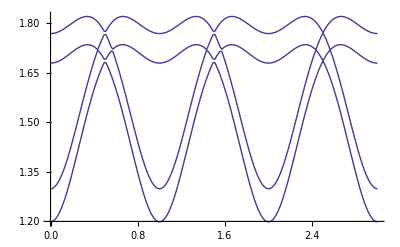

```mathematica
Plot[symplecticSpectrum[testHam[{h,0.0,0.5}*(2Pi)]],
{h,0,3},
PerformanceGoal->"Speed"
]
```

```mathematica
points=Reap[
Plot[symplecticSpectrum[testHam[{h,0.0,0.5}*(2Pi)]],
{h,0,3},
PerformanceGoal->"Speed",
EvaluationMonitor:>Sow[h]]
]⟦-1,1⟧;
```

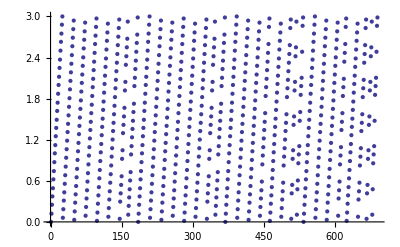

```mathematica
ListPlot[points]
```

```mathematica
?Unevaluated
```

Unevaluated[expr] represents the unevaluated form of expr when it appears as the argument to a function.

```mathematica
makeSpinsFn[crystal_,couplingRules_,classicalSpinFn_]:=
Function[{tau,Qhat},
Evaluate[
Tr[
polarization[Qhat].Transpose[
Outer[Times,#,#,2]&[
στVector[crystal]~replace~{
ϕRules,
couplingRules,
classicalSpinFn[couplingRules],
{𝓈->2,τ->tau}}
],
{3,1,4,2}],
Plus,2]
]];
```

```mathematica
makeSpinsFn[Γ4,testCouplings,ghettoSpinFn]
```

Part::partd: Part specification {Qhkl, Qhkl - Qhkl . {{0.774956, 0., 0.}, {0., 0.774956, 0.}, {0., 0., 0.614}}} ⟦ 1, 1 ⟧ is longer than depth of object.

Part::partd: Part specification {Qhkl, Qhkl - Qhkl . {{0.774956, 0., 0.}, {0., 0.774956, 0.}, {0., 0., 0.614}}} ⟦ 1, 2 ⟧ is longer than depth of object.

Part::partd: Part specification {Qhkl, Qhkl - Qhkl . {{0.774956, 0., 0.}, {0., 0.774956, 0.}, {0., 0., 0.614}}} ⟦ 1, 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Function::flpar: Parameter specification {Qhkl_List} in Function[{Qhkl_List}, {{(-0.00173676 + 0.\ ⅈ)\ ⅇ^-2\ ⅈ\ π\ Plus[« 3 »]\ (1 - Power[« 2 »]) + (0.0415294  + 0.\ ⅈ)\ ⅇ^-2\ ⅈ\ π\ Plus[« 3 »]\ Qhkl . {« 3 »}/Abs[« 1 »][1]\ Qhkl . {« 3 »}/Abs[« 1 »][2] - (0.248263  + 0.\ ⅈ)\ ⅇ^-2\ ⅈ\ π\ Plus[« 3 »]\ (1 - Power[« 2 »]) - (0.  + 0.0416744\ ⅈ)\ ⅇ^« 1 »\ Qhkl « 1 » {« 1 » « 1 »/Abs[« 1 »][1]\ Qhkl . {« 3 »}/Abs[« 1 »][3] - (0.  + 0.49826\ ⅈ)\ ⅇ^-2\ ⅈ\ π\ Plus[« 3 »]\ Qhkl . {« 3 »}/Abs[« 1 »][2]\ Qhkl . {« 3 »}/Abs[« 1 »][3] + 1/4\ ⅇ^-2\ ⅈ\ π\ Plus[« 3 »]\ (1 - Power[« 2 »]), « 14 », « 1 »}, « 15 »}]
 should be a symbol or a list of symbols.

Function[{Qhkl_List},{«1»}]

```mathematica
testSpins=makeSpinsFn[Γ4,testCouplings,ghettoSpinFn];
```

Part::partd: Part specification tau$ ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification tau$ ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification tau$ ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

```mathematica
incoherentCrossSection[{0.3,0,0.5},2.0,testHam,testSpins,Γ4]//Chop
```

{0.708975,0.639381,0.654344,0.958634}

```mathematica
testSpins[{0,0,0},Normalize[{0.3,0,0.5}]]//Dimensions
```

{16,16}

```mathematica
?Plot
```

Plot[f,{x,x_min,x_max}] generates a plot of f as a function of x from x_min to x_max. 
Plot[{f_1,f_2,…},{x,x_min,x_max}] plots several functions f_i.

```mathematica
Thread[{a,{b,bb},{c,cc}}]
```

{{a,b,c},{a,bb,cc}}

```mathematica
testData=Table[
Thread[{h,
4*symplecticSpectrum[testHam[{h,0.0,0.5}*(2Pi)]],
incoherentCrossSection[{0.3,0,0.5}*(2Pi),2.0,testHam,testSpins,Γ4]
}],
{h,0.001,3.0,0.05}];
```

```mathematica
Dimensions[Transpose[testData,{2,1,3}]]
```

{4,60,3}

```mathematica
Re[Chop[Transpose[testData,{2,1,3}]]][[All,-1,All]]
```

{{2.951,7.08667,0.726902},{2.951,6.72941,0.974073},{2.951,5.23488,0.534844},{2.951,4.83548,0.255966}}

```mathematica
ListPointPlot3D[Re[Chop[Transpose[testData,{2,1,3}]]],
Filling->Bottom,
ColorFunction->"Rainbow",
PlotRange->{{0,3},All,All},
AxesLabel->{"𝒬=(𝒽,0,1/2) (rlu)","ℏω","Intensity"}]
```

-Graphics3D-

```mathematica
hamMat//TrigExpand
```

{{0,0,0,0,0,«6»,0,0,0,0,0},{0,0,0,0,«8»,0,0,0,0},{0,0,0,0,1/2 tt Cos[π 𝓆[3]]-1/2 tt Cos[β/2] Cos[δ] Cos[π 𝓆[3]]+1/2 tt Cos[π 𝓆[3]] Sin[β/2] Sin[δ],λ/2,0,1/4 Cos[β/2] Cos[γ] Cos[π (-𝓆[1]/2-𝓆[2]/2)]^2+«16»+1/4 Sin[β/2] Sin[γ] Sin[π (𝓆[1]/2-𝓆[2]/2)]^2,-1/4 Cos[β/2] Cos[γ] Cos[«1»]^2+«16»,0,λ/2+Cos[β/4]^2 Cos[γ/2]^2-tt Cos[β/4]^2 Cos[δ/2]^2+«38»,1/2 tt Cos[π 𝓆[3]]+1/2 tt Cos[β/2] Cos[δ] Cos[π 𝓆[3]]-1/2 tt Cos[π 𝓆[3]] Sin[β/2] Sin[δ],0,0,0,0},«11»,{0,0,0,0,«8»,0,0,0,0},{0,0,0,0,0,«6»,0,0,0,0,0}}

```mathematica
στVector[Γ4]//TrigExpand
```

{{-(ⅇ^(-ⅈ π (τ[1]+τ[2]+τ[3])) √𝓈 Cos[ϕ[2,0,0,1]] Sin[θ[2,0,0,1]])/(2 √2)+(ⅈ ⅇ^(-ⅈ π (τ[1]+τ[2]+τ[3])) √𝓈 Sin[ϕ[2,0,0,1]])/(2 √2),-(ⅈ ⅇ^(-ⅈ π (τ[1]+τ[2]+τ[3])) √𝓈 Cos[ϕ[2,0,0,1]])/(2 √2)-(ⅇ^(-ⅈ π (τ[1]+τ[2]+τ[3])) √𝓈 Sin[θ[2,0,0,1]] Sin[ϕ[2,0,0,1]])/(2 √2),(ⅇ^(-ⅈ π (τ[1]+τ[2]+τ[3])) √𝓈 Cos[θ[2,0,0,1]])/(2 √2)},{-(ⅇ^(-ⅈ π (τ[1]+τ[2])) √𝓈 Cos[ϕ[2,0,0,0]] Sin[θ[2,0,0,0]])/(2 √2)+(ⅈ ⅇ^(-ⅈ π (τ[1]+τ[2])) √𝓈 Sin[ϕ[2,0,0,0]])/(2 √2),-(ⅈ ⅇ^(-ⅈ π (τ[1]+τ[2])) √𝓈 Cos[ϕ[2,0,0,0]])/(2 √2)-(ⅇ^(-ⅈ π (τ[1]+τ[2])) √𝓈 Sin[θ[2,0,0,0]] Sin[ϕ[2,0,0,0]])/(2 √2),(ⅇ^(-ⅈ π (τ[1]+τ[2])) √𝓈 Cos[θ[2,0,0,0]])/(2 √2)},{-(ⅇ^(-ⅈ π τ[3]) √𝓈 Cos[ϕ[1,0,0,1]] Sin[θ[1,0,0,1]])/(2 √2)+(ⅈ ⅇ^(-ⅈ π τ[3]) √𝓈 Sin[ϕ[1,0,0,1]])/(2 √2),-(ⅈ ⅇ^(-ⅈ π τ[3]) √𝓈 Cos[ϕ[1,0,0,1]])/(2 √2)-(ⅇ^(-ⅈ π τ[3]) √𝓈 Sin[θ[1,0,0,1]] Sin[ϕ[1,0,0,1]])/(2 √2),(ⅇ^(-ⅈ π τ[3]) √𝓈 Cos[θ[1,0,0,1]])/(2 √2)},{-(√𝓈 Cos[ϕ[1,0,0,0]] Sin[θ[1,0,0,0]])/(2 √2)+(ⅈ √𝓈 Sin[ϕ[1,0,0,0]])/(2 √2),-(ⅈ √𝓈 Cos[ϕ[1,0,0,0]])/(2 √2)-(√𝓈 Sin[θ[1,0,0,0]] Sin[ϕ[1,0,0,0]])/(2 √2),(√𝓈 Cos[θ[1,0,0,0]])/(2 √2)},{-(√𝓈 Cos[ϕ[1,0,0,0]] Sin[θ[1,0,0,0]])/(2 √2)+(ⅈ √𝓈 Sin[ϕ[1,0,0,0]])/(2 √2),-(ⅈ √𝓈 Cos[ϕ[1,0,0,0]])/(2 √2)-(√𝓈 Sin[θ[1,0,0,0]] Sin[ϕ[1,0,0,0]])/(2 √2),(√𝓈 Cos[θ[1,0,0,0]])/(2 √2)},{-(ⅇ^(ⅈ π τ[3]) √𝓈 Cos[ϕ[1,0,0,1]] Sin[θ[1,0,0,1]])/(2 √2)+(ⅈ ⅇ^(ⅈ π τ[3]) √𝓈 Sin[ϕ[1,0,0,1]])/(2 √2),-(ⅈ ⅇ^(ⅈ π τ[3]) √𝓈 Cos[ϕ[1,0,0,1]])/(2 √2)-(ⅇ^(ⅈ π τ[3]) √𝓈 Sin[θ[1,0,0,1]] Sin[ϕ[1,0,0,1]])/(2 √2),(ⅇ^(ⅈ π τ[3]) √𝓈 Cos[θ[1,0,0,1]])/(2 √2)},{-(ⅇ^(ⅈ π (τ[1]+τ[2])) √𝓈 Cos[ϕ[2,0,0,0]] Sin[θ[2,0,0,0]])/(2 √2)+(ⅈ ⅇ^(ⅈ π (τ[1]+τ[2])) √𝓈 Sin[ϕ[2,0,0,0]])/(2 √2),-(ⅈ ⅇ^(ⅈ π (τ[1]+τ[2])) √𝓈 Cos[ϕ[2,0,0,0]])/(2 √2)-(ⅇ^(ⅈ π (τ[1]+τ[2])) √𝓈 Sin[θ[2,0,0,0]] Sin[ϕ[2,0,0,0]])/(2 √2),(ⅇ^(ⅈ π (τ[1]+τ[2])) √𝓈 Cos[θ[2,0,0,0]])/(2 √2)},{-(ⅇ^(ⅈ π (τ[1]+τ[2]+τ[3])) √𝓈 Cos[ϕ[2,0,0,1]] Sin[θ[2,0,0,1]])/(2 √2)+(ⅈ ⅇ^(ⅈ π (τ[1]+τ[2]+τ[3])) √𝓈 Sin[ϕ[2,0,0,1]])/(2 √2),-(ⅈ ⅇ^(ⅈ π (τ[1]+τ[2]+τ[3])) √𝓈 Cos[ϕ[2,0,0,1]])/(2 √2)-(ⅇ^(ⅈ π (τ[1]+τ[2]+τ[3])) √𝓈 Sin[θ[2,0,0,1]] Sin[ϕ[2,0,0,1]])/(2 √2),(ⅇ^(ⅈ π (τ[1]+τ[2]+τ[3])) √𝓈 Cos[θ[2,0,0,1]])/(2 √2)},{-(ⅇ^(ⅈ π (τ[1]+τ[2]+τ[3])) √𝓈 Cos[ϕ[2,0,0,1]] Sin[θ[2,0,0,1]])/(2 √2)-(ⅈ ⅇ^(ⅈ π (τ[1]+τ[2]+τ[3])) √𝓈 Sin[ϕ[2,0,0,1]])/(2 √2),(ⅈ ⅇ^(ⅈ π (τ[1]+τ[2]+τ[3])) √𝓈 Cos[ϕ[2,0,0,1]])/(2 √2)-(ⅇ^(ⅈ π (τ[1]+τ[2]+τ[3])) √𝓈 Sin[θ[2,0,0,1]] Sin[ϕ[2,0,0,1]])/(2 √2),(ⅇ^(ⅈ π (τ[1]+τ[2]+τ[3])) √𝓈 Cos[θ[2,0,0,1]])/(2 √2)},{-(ⅇ^(ⅈ π (τ[1]+τ[2])) √𝓈 Cos[ϕ[2,0,0,0]] Sin[θ[2,0,0,0]])/(2 √2)-(ⅈ ⅇ^(ⅈ π (τ[1]+τ[2])) √𝓈 Sin[ϕ[2,0,0,0]])/(2 √2),(ⅈ ⅇ^(ⅈ π (τ[1]+τ[2])) √𝓈 Cos[ϕ[2,0,0,0]])/(2 √2)-(ⅇ^(ⅈ π (τ[1]+τ[2])) √𝓈 Sin[θ[2,0,0,0]] Sin[ϕ[2,0,0,0]])/(2 √2),(ⅇ^(ⅈ π (τ[1]+τ[2])) √𝓈 Cos[θ[2,0,0,0]])/(2 √2)},{-(ⅇ^(ⅈ π τ[3]) √𝓈 Cos[ϕ[1,0,0,1]] Sin[θ[1,0,0,1]])/(2 √2)-(ⅈ ⅇ^(ⅈ π τ[3]) √𝓈 Sin[ϕ[1,0,0,1]])/(2 √2),(ⅈ ⅇ^(ⅈ π τ[3]) √𝓈 Cos[ϕ[1,0,0,1]])/(2 √2)-(ⅇ^(ⅈ π τ[3]) √𝓈 Sin[θ[1,0,0,1]] Sin[ϕ[1,0,0,1]])/(2 √2),(ⅇ^(ⅈ π τ[3]) √𝓈 Cos[θ[1,0,0,1]])/(2 √2)},{-(√𝓈 Cos[ϕ[1,0,0,0]] Sin[θ[1,0,0,0]])/(2 √2)-(ⅈ √𝓈 Sin[ϕ[1,0,0,0]])/(2 √2),(ⅈ √𝓈 Cos[ϕ[1,0,0,0]])/(2 √2)-(√𝓈 Sin[θ[1,0,0,0]] Sin[ϕ[1,0,0,0]])/(2 √2),(√𝓈 Cos[θ[1,0,0,0]])/(2 √2)},{-(√𝓈 Cos[ϕ[1,0,0,0]] Sin[θ[1,0,0,0]])/(2 √2)-(ⅈ √𝓈 Sin[ϕ[1,0,0,0]])/(2 √2),(ⅈ √𝓈 Cos[ϕ[1,0,0,0]])/(2 √2)-(√𝓈 Sin[θ[1,0,0,0]] Sin[ϕ[1,0,0,0]])/(2 √2),(√𝓈 Cos[θ[1,0,0,0]])/(2 √2)},{-(ⅇ^(-ⅈ π τ[3]) √𝓈 Cos[ϕ[1,0,0,1]] Sin[θ[1,0,0,1]])/(2 √2)-(ⅈ ⅇ^(-ⅈ π τ[3]) √𝓈 Sin[ϕ[1,0,0,1]])/(2 √2),(ⅈ ⅇ^(-ⅈ π τ[3]) √𝓈 Cos[ϕ[1,0,0,1]])/(2 √2)-(ⅇ^(-ⅈ π τ[3]) √𝓈 Sin[θ[1,0,0,1]] Sin[ϕ[1,0,0,1]])/(2 √2),(ⅇ^(-ⅈ π τ[3]) √𝓈 Cos[θ[1,0,0,1]])/(2 √2)},{-(ⅇ^(-ⅈ π (τ[1]+τ[2])) √𝓈 Cos[ϕ[2,0,0,0]] Sin[θ[2,0,0,0]])/(2 √2)-(ⅈ ⅇ^(-ⅈ π (τ[1]+τ[2])) √𝓈 Sin[ϕ[2,0,0,0]])/(2 √2),(ⅈ ⅇ^(-ⅈ π (τ[1]+τ[2])) √𝓈 Cos[ϕ[2,0,0,0]])/(2 √2)-(ⅇ^(-ⅈ π (τ[1]+τ[2])) √𝓈 Sin[θ[2,0,0,0]] Sin[ϕ[2,0,0,0]])/(2 √2),(ⅇ^(-ⅈ π (τ[1]+τ[2])) √𝓈 Cos[θ[2,0,0,0]])/(2 √2)},{-(ⅇ^(-ⅈ π (τ[1]+τ[2]+τ[3])) √𝓈 Cos[ϕ[2,0,0,1]] Sin[θ[2,0,0,1]])/(2 √2)-(ⅈ ⅇ^(-ⅈ π (τ[1]+τ[2]+τ[3])) √𝓈 Sin[ϕ[2,0,0,1]])/(2 √2),(ⅈ ⅇ^(-ⅈ π (τ[1]+τ[2]+τ[3])) √𝓈 Cos[ϕ[2,0,0,1]])/(2 √2)-(ⅇ^(-ⅈ π (τ[1]+τ[2]+τ[3])) √𝓈 Sin[θ[2,0,0,1]] Sin[ϕ[2,0,0,1]])/(2 √2),(ⅇ^(-ⅈ π (τ[1]+τ[2]+τ[3])) √𝓈 Cos[θ[2,0,0,1]])/(2 √2)}}

## Debugging: making sure MFT4/MFT5 give same minimization equations, etc. -- PASSES

### MFT4

```mathematica
ϕMat=Inverse[(1/2)*{(1/2){1,1,1,1},2*{1,-1,-1,1},{-1,1,-1,1},{1,1,-1,-1}}];
ϕRules={θ[_]->0,ϕ[i_]:>(ϕMat.{α+χ,β,γ+Φ+Pi,δ})⟦i⟧};
```

#### try1: simple lattice

```mathematica
foo2=(1/(𝓈(𝓈+1)ε2*Cos[Θ]))(
𝓈(𝓈+1)planarHeisenberg[{jxy,jz},Γ2]
+𝓈(𝓈+1)dz*dzyaloshinskiMoriya[Γ2]
)~replace~{{θ[_]->0},reducedParams1,reducedParams2};
TrigReduce[Expand[TrigExpand[
D[foo2,#]&/@{ϕ[1],ϕ[2]}
]]]
```

{-2 Sin[Φ+ϕ[1]-ϕ[2]],2 Sin[Φ+ϕ[1]-ϕ[2]]}

```mathematica
{hpHam0,hpHam1,hpHam2}=
makeHamiltonian[{
hpPlanarHeisenberg[{jxy,jz},Γ2],
dz*hpDzyaloshinskiMoriya[Γ2]
},{θ[_]->0},Γ2];
linearCoeffs[Sqrt[2]/(𝓈*I*Sqrt[𝓈])*hpHam1]⟦{1,3}⟧
```

{-2 Sin[Φ+ϕ[1]-ϕ[2]],2 Sin[Φ+ϕ[1]-ϕ[2]]}

#### try2: right lattice (maybe a problem with supercell??

```mathematica
foo2=(1/(𝓈(𝓈+1)ε2*Cos[Θ]))(
𝓈(𝓈+1)planarHeisenberg[{jxy,jz},Γ4]
+𝓈(𝓈+1)dz*dzyaloshinskiMoriya[Γ4]
)~replace~{ϕRules,reducedParams1,reducedParams2};
(test1=Collect[
TrigExpand[
D[foo2,#]&/@{α,β,γ,δ}
]/.Tan[Θ]->tt,
tt|𝒽,TrigFactor]//Simplify)//TableForm
```

0
(Cos[γ]-tt Cos[δ]) Sin[β/2]
2 Cos[β/2] Sin[γ]
-2 tt Cos[β/2] Sin[δ]

```mathematica
{hpHam0,hpHam1,hpHam2}=
makeHamiltonian[{
hpPlanarHeisenberg[{jxy,jz},Γ4],
dz*hpDzyaloshinskiMoriya[Γ4]
},ϕRules,Γ4];
(test2=Collect[
Inverse[ϕMat].(
TrigExpand[linearCoeffs[
Sqrt[2]/(𝓈*I*Sqrt[𝓈])*hpHam1]⟦{1,3,5,7}⟧
]/.Tan[Θ]->tt
),
tt|𝒽,TrigFactor]//Simplify)//TableForm
```

0
4 (Cos[γ]-tt Cos[δ]) Sin[β/2]
2 Cos[β/2] Sin[γ]
-2 tt Cos[β/2] Sin[δ]

```mathematica
test1-({-4,1/4,1,1}*test2)//Expand//TrigExpand
```

{0,0,0,0}

#### try3: whole thing

```mathematica
foo2=(1/(𝓈(𝓈+1)ε2*Cos[Θ]))(
𝓈(𝓈+1)planarHeisenberg[{jxy,jz},Γ4]
+𝓈(𝓈+1)dz*dzyaloshinskiMoriya[Γ4]
-gμB(𝓈+1)zeeman[{hx,hy,0},Γ4]+
gsμB(𝓈+1)anisotropicZ[{hx,hy,0},Γ4]+
Λ*𝓈(𝓈+1)easyPlane[Γ4]
)~replace~{ϕRules,reducedParams1,reducedParams2};
(test1=Collect[
TrigExpand[
D[foo2,#]&/@{α,β,γ,δ}
]/.Tan[Θ]->tt,
tt|𝒽,TrigFactor]//Simplify)//TableForm
```

𝒽 (-Cos[1/4 (4 α-β-2 (γ+δ-ξ))]+Cos[1/4 (4 α-β+2 (γ+δ-ξ))]-2 Sin[α+β/4] Sin[1/2 (γ-δ-ξ)])
1/4 (𝒽 Cos[1/4 (4 α-β-2 (γ+δ-ξ))]-𝒽 Cos[1/4 (4 α-β+2 (γ+δ-ξ))]+𝒽 Cos[1/4 (4 α+β+2 γ-2 δ-2 ξ)]-𝒽 Cos[1/4 (4 α+β+2 (-γ+δ+ξ))]+2 Sin[1/2 (β-2 γ)]+2 Sin[β/2+γ]-2 tt Sin[1/2 (β-2 δ)]-2 tt Sin[β/2+δ])
1/2 𝒽 (Cos[1/4 (4 α-β-2 (γ+δ-ξ))]+Cos[1/4 (4 α-β+2 (γ+δ-ξ))]+2 Cos[α+β/4] Cos[1/2 (γ-δ-ξ)])+2 Cos[β/2] Sin[γ]
1/2 𝒽 (Cos[1/4 (4 α-β-2 (γ+δ-ξ))]+Cos[1/4 (4 α-β+2 (γ+δ-ξ))]-2 Cos[α+β/4] Cos[1/2 (γ-δ-ξ)])-2 tt Cos[β/2] Sin[δ]

```mathematica
{hpHam0,hpHam1,hpHam2}=
makeHamiltonian[{
hpPlanarHeisenberg[{jxy,jz},Γ4],
dz*hpDzyaloshinskiMoriya[Γ4],
-gμB*hpZeeman[{hx,hy,0},Γ4],
gsμB*hpAnisotropicZ[{hx,hy,0},Γ4],
Λ*hpEasyPlane[Γ4]
},ϕRules,Γ4];
(test2=Collect[
Inverse[ϕMat].(
TrigExpand[linearCoeffs[
Sqrt[2]/(𝓈*I*Sqrt[𝓈])*hpHam1]⟦{1,3,5,7}⟧
]/.Tan[Θ]->tt
),
tt|𝒽,TrigFactor]//Simplify)//TableForm
```

-1/4 𝒽 (Cos[1/4 (4 α-β-2 (γ+δ-ξ))]-Cos[1/4 (4 α-β+2 (γ+δ-ξ))]+2 Sin[α+β/4] Sin[1/2 (γ-δ-ξ)])
𝒽 Cos[1/4 (4 α-β-2 (γ+δ-ξ))]-𝒽 Cos[1/4 (4 α-β+2 (γ+δ-ξ))]+𝒽 Cos[1/4 (4 α+β+2 γ-2 δ-2 ξ)]-𝒽 Cos[1/4 (4 α+β+2 (-γ+δ+ξ))]+2 Sin[1/2 (β-2 γ)]+2 Sin[β/2+γ]-2 tt Sin[1/2 (β-2 δ)]-2 tt Sin[β/2+δ]
1/2 𝒽 (Cos[1/4 (4 α-β-2 (γ+δ-ξ))]+Cos[1/4 (4 α-β+2 (γ+δ-ξ))]+2 Cos[α+β/4] Cos[1/2 (γ-δ-ξ)])+2 Cos[β/2] Sin[γ]
1/2 𝒽 (Cos[1/4 (4 α-β-2 (γ+δ-ξ))]+Cos[1/4 (4 α-β+2 (γ+δ-ξ))]-2 Cos[α+β/4] Cos[1/2 (γ-δ-ξ)])-2 tt Cos[β/2] Sin[δ]

```mathematica
test1-({4,1/4,1,1}*test2)//Expand//TrigExpand
```

{0,0,0,0}

#### check constant term in energy while we’re at it

```mathematica
Collect[
TrigExpand[foo2]/.Tan[Θ]->tt,
tt|𝒽,TrigFactor]//Simplify
```

-Cos[1/2 (β-2 γ)]-Cos[β/2+γ]+tt Cos[1/2 (β-2 δ)]+tt Cos[β/2+δ]-𝒽 Sin[1/4 (4 α-β-2 (γ+δ-ξ))]+𝒽 Sin[1/4 (4 α-β+2 (γ+δ-ξ))]+𝒽 Sin[1/4 (4 α+β+2 γ-2 δ-2 ξ)]-𝒽 Sin[1/4 (4 α+β+2 (-γ+δ+ξ))]

```mathematica
Collect[
TrigExpand[hpHam0]/.Tan[Θ]->tt,
tt|𝒽,TrigFactor]//Simplify
```

-1/2 𝓈 (4 (1+𝓈) Cos[β/2] (Cos[γ]-tt Cos[δ])+𝒽 (1+2 𝓈) (Sin[1/4 (4 α-β-2 (γ+δ-ξ))]-Sin[1/4 (4 α-β+2 (γ+δ-ξ))]-2 Cos[α+β/4] Sin[1/2 (γ-δ-ξ)]))

```mathematica
(-Cos[1/2 (β-2 γ)]-Cos[β/2+γ]+tt Cos[1/2 (β-2 δ)]+tt Cos[β/2+δ]-𝒽 Sin[1/4 (4 α-β-2 (γ+δ-ξ))]+𝒽 Sin[1/4 (4 α-β+2 (γ+δ-ξ))]+𝒽 Sin[1/4 (4 α+β+2 γ-2 δ-2 ξ)]-𝒽 Sin[1/4 (4 α+β+2 (-γ+δ+ξ))])-(1/(𝓈(𝓈+1)))*(-1/2 𝓈 (4 (1+𝓈) Cos[β/2] (Cos[γ]-tt Cos[δ])+𝒽 (1+2 𝓈) (Sin[1/4 (4 α-β-2 (γ+δ-ξ))]-Sin[1/4 (4 α-β+2 (γ+δ-ξ))]-2 Cos[α+β/4] Sin[1/2 (γ-δ-ξ)])))//TrigExpand//Together
```

-1/(1+𝓈)2 (-𝒽 Cos[α] Cos[β/4] Cos[δ/2] Cos[ξ/2] Sin[γ/2]-𝒽 Cos[γ/2] Cos[ξ/2] Sin[α] Sin[β/4] Sin[δ/2]+𝒽 Cos[α] Cos[β/4] Cos[γ/2] Cos[δ/2] Sin[ξ/2]-𝒽 Sin[α] Sin[β/4] Sin[γ/2] Sin[δ/2] Sin[ξ/2])

### MFT5

```mathematica
ϕMat=Inverse[(1/2)*{(1/2){1,1,1,1},2*{1,-1,-1,1},{-1,1,-1,1},{1,1,-1,-1}}];
ϕRules={θ[__]->0,ϕ[i_,0,0,j_]:>(ϕMat.{α+χ,β,γ+Φ+Pi,δ})⟦i+2j⟧};
```

#### try1: simple lattice

```mathematica
Block[{gCrystal=Γ2,gSpins=Classical},
foo2=
(1/(𝓈(𝓈+1)ε2*Cos[Θ]))(
planarHeisenberg[{jxy,jz}]+
dz*dzyaloshinskiMoriya[]
)~replace~{ϕRules,reducedParams1,reducedParams2}
];
TrigReduce[Expand[TrigExpand[
D[foo2,#]&/@{ϕ[1],ϕ[2]}
]]]
```

{-2 Sin[Φ+ϕ[1]-ϕ[2]],2 Sin[Φ+ϕ[1]-ϕ[2]]}

```mathematica
Block[{gCrystal=Γ2,gSpins=Quantum},
foo=First@linearCoeffs[
operatorTruncate[
(1/(𝓈(𝓈+1)ε2*Cos[Θ]))(
planarHeisenberg[{jxy,jz}]+
dz*dzyaloshinskiMoriya[]
)~replace~{ϕRules,reducedParams1,reducedParams2},
{1}]
]
];
TrigReduce[Expand[TrigExpand[
foo/.{Tan[Θ]->tt}
]]]
```

{(ⅈ √2 √𝓈 Sin[Φ+ϕ[1]-ϕ[2]])/(1+𝓈),-(ⅈ √2 √𝓈 Sin[Φ+ϕ[1]-ϕ[2]])/(1+𝓈)}

#### try2: right lattice (maybe a problem with supercell??

```mathematica
Block[{gCrystal=Γ4,gSpins=Classical},
foo2=
(1/(𝓈(𝓈+1)ε2*Cos[Θ]))(
planarHeisenberg[{jxy,jz}]+
dz*dzyaloshinskiMoriya[]
)~replace~{ϕRules,reducedParams1,reducedParams2}
];
(test1=Collect[
TrigExpand[
D[foo2,#]&/@{α,β,γ,δ}
]/.Tan[Θ]->tt,
tt|𝒽,TrigFactor]//Simplify)//TableForm
```

0
(Cos[γ]-tt Cos[δ]) Sin[β/2]
2 Cos[β/2] Sin[γ]
-2 tt Cos[β/2] Sin[δ]

```mathematica
Block[{gCrystal=Γ4,gSpins=Quantum},
foo=First@linearCoeffs[
operatorTruncate[
(1/(𝓈(𝓈+1)ε2*Cos[Θ]))(
planarHeisenberg[{jxy,jz}]+
dz*dzyaloshinskiMoriya[]
)~replace~{ϕRules,reducedParams1,reducedParams2},
{1}]
]
];
(test2=Collect[
Inverse[ϕMat].(
Sqrt[2](𝓈+1)/(I*Sqrt[𝓈])*
TrigExpand[foo]/.Tan[Θ]->tt
),
tt|𝒽,TrigFactor]//Simplify)//TableForm
```

0
-4 (Cos[γ]-tt Cos[δ]) Sin[β/2]
-2 tt Cos[β/2] Sin[δ]
2 Cos[β/2] Sin[γ]

```mathematica
test1-({-4,-1/4,1,1}*test2⟦{1,2,4,3}⟧)//Expand//TrigExpand
```

{0,0,0,0}

#### try3: whole thing

```mathematica
Block[{gCrystal=Γ4,gSpins=Classical},
foo2=
(1/(𝓈(𝓈+1)ε2*Cos[Θ]))(
planarHeisenberg[{jxy,jz}]+
dz*dzyaloshinskiMoriya[]+
-gμB*zeeman[{hx,hy,0}]+
gsμB*anisotropicZ[{hx,hy,0}]+
Λ*easyPlane[]
)~replace~{ϕRules,reducedParams1,reducedParams2}
];
(test1=Collect[
TrigExpand[
D[foo2,#]&/@{α,β,γ,δ}
]/.Tan[Θ]->tt,
tt|𝒽,TrigReduce])//TableForm
```

𝒽 (Cos[α+β/4+γ/2-δ/2-ξ/2]+Cos[α-β/4+γ/2+δ/2-ξ/2]-Cos[α-β/4-γ/2-δ/2+ξ/2]-Cos[α+β/4-γ/2+δ/2+ξ/2])
1/4 𝒽 (Cos[α+β/4+γ/2-δ/2-ξ/2]-Cos[α-β/4+γ/2+δ/2-ξ/2]+Cos[α-β/4-γ/2-δ/2+ξ/2]-Cos[α+β/4-γ/2+δ/2+ξ/2])+1/2 (Sin[β/2-γ]+Sin[β/2+γ])+1/2 tt (-Sin[β/2-δ]-Sin[β/2+δ])
1/2 𝒽 (Cos[α+β/4+γ/2-δ/2-ξ/2]+Cos[α-β/4+γ/2+δ/2-ξ/2]+Cos[α-β/4-γ/2-δ/2+ξ/2]+Cos[α+β/4-γ/2+δ/2+ξ/2])-Sin[β/2-γ]+Sin[β/2+γ]
1/2 𝒽 (-Cos[α+β/4+γ/2-δ/2-ξ/2]+Cos[α-β/4+γ/2+δ/2-ξ/2]+Cos[α-β/4-γ/2-δ/2+ξ/2]-Cos[α+β/4-γ/2+δ/2+ξ/2])+tt (Sin[β/2-δ]-Sin[β/2+δ])

```mathematica
Block[{gCrystal=Γ4,gSpins=Quantum},
foo=First@linearCoeffs[
operatorTruncate[
(1/(𝓈(𝓈+1)ε2*Cos[Θ]))(
planarHeisenberg[{jxy,jz}]+
dz*dzyaloshinskiMoriya[]+
-gμB*zeeman[{hx,hy,0}]+
gsμB*anisotropicZ[{hx,hy,0}]+
Λ*easyPlane[]
)~replace~{ϕRules,reducedParams1,reducedParams2},
{1}]
]
];
(test2=Collect[
Inverse[ϕMat].(
Sqrt[2](𝓈+1)/(I*Sqrt[𝓈])*
TrigExpand[foo]/.Tan[Θ]->tt
),
tt|𝒽,TrigReduce])//TableForm
```

1/4 𝒽 (-Cos[α+β/4+γ/2-δ/2-ξ/2]-Cos[α-β/4+γ/2+δ/2-ξ/2]+Cos[α-β/4-γ/2-δ/2+ξ/2]+Cos[α+β/4-γ/2+δ/2+ξ/2])
𝒽 (-Cos[α+β/4+γ/2-δ/2-ξ/2]+Cos[α-β/4+γ/2+δ/2-ξ/2]-Cos[α-β/4-γ/2-δ/2+ξ/2]+Cos[α+β/4-γ/2+δ/2+ξ/2])-2 (Sin[β/2-γ]+Sin[β/2+γ])+2 tt (Sin[β/2-δ]+Sin[β/2+δ])
1/2 𝒽 (-Cos[α+β/4+γ/2-δ/2-ξ/2]+Cos[α-β/4+γ/2+δ/2-ξ/2]+Cos[α-β/4-γ/2-δ/2+ξ/2]-Cos[α+β/4-γ/2+δ/2+ξ/2])+tt (Sin[β/2-δ]-Sin[β/2+δ])
1/2 𝒽 (Cos[α+β/4+γ/2-δ/2-ξ/2]+Cos[α-β/4+γ/2+δ/2-ξ/2]+Cos[α-β/4-γ/2-δ/2+ξ/2]+Cos[α+β/4-γ/2+δ/2+ξ/2])-Sin[β/2-γ]+Sin[β/2+γ]

```mathematica
test1-({-4,-1/4,1,1}*test2⟦{1,2,4,3}⟧)//Expand//TrigExpand
```

{0,0,0,0}

#### check constant term in energy while we’re at it

```mathematica
Collect[
TrigExpand[foo2]/.Tan[Θ]->tt,
tt|𝒽,TrigFactor]//Simplify
```

-Cos[1/2 (β-2 γ)]-Cos[β/2+γ]+tt Cos[1/2 (β-2 δ)]+tt Cos[β/2+δ]-𝒽 Sin[1/4 (4 α-β-2 (γ+δ-ξ))]+𝒽 Sin[1/4 (4 α-β+2 (γ+δ-ξ))]+𝒽 Sin[1/4 (4 α+β+2 γ-2 δ-2 ξ)]-𝒽 Sin[1/4 (4 α+β+2 (-γ+δ+ξ))]

```mathematica
Collect[
TrigExpand[
Block[{gCrystal=Γ4,gSpins=Quantum},
foo=operatorTruncate[
(1/(𝓈(𝓈+1)ε2*Cos[Θ]))(
planarHeisenberg[{jxy,jz}]+
dz*dzyaloshinskiMoriya[]+
-gμB*zeeman[{hx,hy,0}]+
gsμB*anisotropicZ[{hx,hy,0}]+
Λ*easyPlane[]
)~replace~{ϕRules,reducedParams1,reducedParams2},
{0}]
]
]/.Tan[Θ]->tt,
tt|𝒽,TrigFactor]//Simplify
```

-1/(1+𝓈)𝓈 (Cos[1/2 (β-2 γ)]+Cos[β/2+γ]-tt Cos[1/2 (β-2 δ)]-tt Cos[β/2+δ]+𝒽 Sin[1/4 (4 α-β-2 (γ+δ-ξ))]-𝒽 Sin[1/4 (4 α-β+2 (γ+δ-ξ))]-𝒽 Sin[1/4 (4 α+β+2 γ-2 δ-2 ξ)]+𝒽 Sin[1/4 (4 α+β+2 (-γ+δ+ξ))])

```mathematica
Out[245]-(𝓈+1)/𝓈*Out[246]//Expand
```

0